### Trophic transmission model

Let D_1 and D_2 be two definitive hosts and N be prey of both and intermediate host. One touchy bit is how to deal with ingestion and predator population growth. One way would be to assume a standard predator-prey model, with predator (definitive host) growth determined entirely by ingestion of prey (intermediate host). Another would be to assume logistic growth of the predator and exponential growth of the prey (or logistic growth of the prey), with predation entering only as mortality of the prey. The second option would make the model more similar to the model used above. There are also issues with embedding an epidemiological model in a predator-prey model with stability of the predator-prey system. For example, a Lotka-Volterra-type formulation will make the system unstable. I will first explore the second option, and then maybe return to a “true” predator-prey model.

#### Model with density-independent intermediate host (prey) growth

Prey (whether infected or not) are eaten by both hosts (whether that results in infection or not). This introduces a challenge: what happens when a definitive host that is already infected eats an intermediate host infected with another strain? Here I am assuming a priority effect: once a definitive host has been infected, it may consume infected intermediate hosts, but that has no effect on its infection status. This differs from the behavior of the parasites in the environment, which are assumed to encounter only susceptible intermediate hosts, and to never encounter infected intermediate hosts.

```mathematica
dNsdt=rN (Ns+Nir+Nim)-a1 Ns (D1s+D1ir+D1im)-a2 Ns (D2s+D2im)-β Ns (Pr+Pm);
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim);
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim;

dNirdt=β Ns Pr-a1 Nir (D1s+D1ir+D1im)-a2 Nir(D2s+D2im)-μN Nir;
dNimdt=β Ns Pm-a1 Nim(D1s+D1ir+D1im)-a2 Nim(D2s+D2im)-μN Nim;

dD1irdt=a1 D1s Nir-μ1 D1ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;

dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β Ns Pm-γ Pm;
```

```mathematica
J={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,D2s],D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr],D[dNsdt,Nim],D[dNsdt,D1im],D[dNsdt,D2im],D[dNsdt,Pm]},
{D[dD1sdt,Ns], D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,Ns], D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,Ns], D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,Ns], D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,Ns], D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,Ns], D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s)-a2 D2s+rN-Pr β | -a1 Ns | -a2 Ns | rN | -a1 Ns | -Ns β | rN | -a1 Ns | -a2 Ns | -Ns β
0 | -a1 Nir+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
Pr β | -a1 Nir | -a2 Nir | -a1 (D1ir+D1s)-a2 D2s-μN | -a1 Nir | Ns β | 0 | -a1 Nir | -a2 Nir | 0
0 | a1 Nir | 0 | a1 D1s | -μ1 | 0 | 0 | 0 | 0 | 0
-Pr β | 0 | 0 | 0 | λ1 | -Ns β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s)-a2 D2s-μN | 0 | 0 | Ns β
0 | 0 | 0 | 0 | 0 | 0 | a1 D1s | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a2 D2s | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -Ns β-γ)

Because J is block triangular, the eigenvalues are given by the eigenvalues of the matrices on the diagonal. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below. Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue:
(a^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1s+a2 D2s)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3))>1

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
F={{0,0,0,Ns β},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 D1s+a1 D1ir+a2 D2s+μN,0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,Ns β+γ}};
(J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β Ns)/(β Ns+γ) ((a1 D1s)/(a1 D1s+a1 D1ir+a2 D2s+μN) (c λ1)/μ1+(a2 D2s)/(a1 D1s+a1 D1ir+a2 D2s+μN) (c λ2)/μ2)//Simplify
```

(-a1 (D1ir+D1s)-a2 D2s-μN | 0 | 0 | Ns β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -Ns β-γ)

True

{0,(c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3)),-((-1)^(1/3) c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3)),((-1)^(2/3) c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3))}

True

The invasion fitness depends on OverHat[N_s], OverHat[D_(1s)], and OverHat[D_(2s)], the equilibria set by the resident parasite.

```mathematica
dNsdt=rN (Ns+Nir)-a1 Ns (D1s+D1ir)-a2 Ns K2-β Ns Pr;
dNirdt=β Ns Pr-a1 Nir (D1s+D1ir)-a2 Nir K2-μN Nir;
dD1sdt=r1 (D1s+D1ir) (1-(D1s+D1ir)/K1)-a1 D1s Nir;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

```mathematica
D1irEq=Solve[dPrdt==0,D1ir][[1]]
```

{D1ir→(Ns Pr β+Pr γ)/λ1}

```mathematica
NirEq=Solve[(dD1irdt/.D1irEq)==0,Nir][[1]]
```

{Nir→((Ns Pr β+Pr γ) μ1)/(a1 D1s λ1)}

```mathematica
NsEq=Solve[(dD1sdt/.D1irEq/.NirEq)==0,Ns][[2]]
```

{Ns→(-2 Pr^2 r1 β γ-2 D1s Pr r1 β λ1+K1 Pr r1 β λ1-K1 Pr β λ1 μ1+√K1 Pr β λ1 √(K1 r1^2+4 D1s r1 μ1-2 K1 r1 μ1+K1 μ1^2))/(2 Pr^2 r1 β^2)}

```mathematica
Solve[(dNirdt/.D1irEq/.NirEq/.NsEq)==0,D1s]
```

{{D1s→-1/(3 a1 r1 λ1^2)(2 a1 Pr r1 γ λ1-a1 K1 r1 λ1^2-a1 K1 r1 λ1 μ1-2 a2 K2 r1 λ1 μ1+a1 K1 λ1 μ1^2-a1 K1 μ1^3-2 r1 λ1 μ1 μN)-(2^(1/3) (-(1)^2/(a1^2 r1^2)+1/(a1^2 r1)))/(3 λ1^2 (1)^(1/3))+(123+1)^(1/3)/(3 2^(1/3) λ1^2)},{D1s→1},{D1s→-1/(3 a1 r1 λ1^2)+((1)11)/(3 3)-((1+ⅈ 1) 1)/(6 2^(1/3) λ1^2)}}
 |  |  |  |

```mathematica
dNsdt=rN (Ns+Nir)-a1 Ns (D1s+D1ir)-a2 Ns K2-β Ns Pr;
dNirdt=β Ns Pr-a1 Nir (D1s+D1ir)-a2 Nir K2-μN Nir;
dD1sdt=r1 (D1s+D1ir) (1-(D1s+D1ir)/K1)-a1 D1s Nir;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

```mathematica
Jres={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr]},
{D[dD1sdt,Ns], D[dD1sdt,D1s], D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr]}};
```

To figure out which of the possible equilibria is feasible, I need to numerically solve the resident system. However, to appropriately choose parameters, I need to ensure that none of the trivial equilibria are stable. There are several trivial equilibria here. One is the trivial equilibrium where only the predator is present (both the parasite and prey go extinct). This equilibrium will be unstable if r_N>a_1 K_1-a_2 K_2.

```mathematica
Eigenvalues[Jres/.{Ns->0,Nir->0,Pr->0,D1s->K1,D1ir->0}]
```

{-r1,-a1 K1-a2 K2+rN,-γ,-μ1,-a1 K1-a2 K2-μN}

Another equilibrium would be where the parasite has gone extinct but the predator and prey coexist. This equilibrium has the same instability condition as above.

```mathematica
Eigenvalues[Jres/.{Nir->0,Pr->0,D1s->K1,D1ir->0}]
```

{-r1,-a1 K1-a2 K2+rN,Root[-a1 K1 Ns β λ1+a1 K1 Ns β μ1+a2 K2 Ns β μ1+a1 K1 γ μ1+a2 K2 γ μ1+Ns β μ1 μN+γ μ1 μN+(a1 K1 Ns β+a2 K2 Ns β+a1 K1 γ+a2 K2 γ+a1 K1 μ1+a2 K2 μ1+Ns β μ1+γ μ1+Ns β μN+γ μN+μ1 μN) #1+(a1 K1+a2 K2+Ns β+γ+μ1+μN) #1^2+#1^3&,1],Root[-a1 K1 Ns β λ1+a1 K1 Ns β μ1+a2 K2 Ns β μ1+a1 K1 γ μ1+a2 K2 γ μ1+Ns β μ1 μN+γ μ1 μN+(a1 K1 Ns β+a2 K2 Ns β+a1 K1 γ+a2 K2 γ+a1 K1 μ1+a2 K2 μ1+Ns β μ1+γ μ1+Ns β μN+γ μN+μ1 μN) #1+(a1 K1+a2 K2+Ns β+γ+μ1+μN) #1^2+#1^3&,2],Root[-a1 K1 Ns β λ1+a1 K1 Ns β μ1+a2 K2 Ns β μ1+a1 K1 γ μ1+a2 K2 γ μ1+Ns β μ1 μN+γ μ1 μN+(a1 K1 Ns β+a2 K2 Ns β+a1 K1 γ+a2 K2 γ+a1 K1 μ1+a2 K2 μ1+Ns β μ1+γ μ1+Ns β μN+γ μN+μ1 μN) #1+(a1 K1+a2 K2+Ns β+γ+μ1+μN) #1^2+#1^3&,3]}

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];NumSol=NDSolve[({Ns'[t]==rN (Ns[t]+Nir[t])-a1 Ns[t] (D1s[t]+D1ir[t])-a2 Ns[t] K2-β Ns[t] Pr[t],
Nir'[t]==β Ns[t] Pr[t]-a1 Nir[t] (D1s[t]+D1ir[t])-a2 Nir[t] K2-μN Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t],
D1ir'[t]==a1 D1s[t] Nir[t]-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β Ns[t] Pr[t]-γ Pr[t],
Ns[0]==100,
Nir[0]==0,
D1s[0]==10,
D1ir[0]==0,
Pr[0]==10}/.{rN->2,a1->0.1,a2->0.09,K2->9,β->1,μN->0.1,r1->0.1,K1->10,μ1->0.01,λ1->1,γ->0.1}),
{Ns,Nir,D1s,D1ir,Pr},{t,0,100},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
```

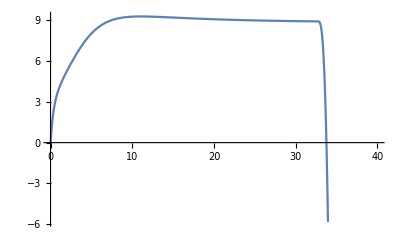

```mathematica
Plot[D1ir[t]/.NumSol,{t,0,40}]
```

This model is infeasible. The reason is because the prey population is guaranteed to either grow exponentially, or to decline to extinction, because the predator population cannot control the prey population: the maximum possible population size for the predators is given by the carrying capacity K. At that carrying capacity, the predator will either be able to drive the prey to exinction (if a_1 K_1+a_2 K_2>r_N) or the prey will grow exponentially. That is why I cannot find any equilibrium.

#### Model with density-dependent intermediate host growth

```mathematica
dNsdt=rN (Ns+Nir+Nim)(1-(Ns+Nir+Nim)/KN)-a1 Ns (D1s+D1ir+D1im)-a2 Ns (D2s+D2im)-β Ns (Pr+Pm);
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim);
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim;

dNirdt=β Ns Pr-a1 Nir (D1s+D1ir+D1im)-a2 Nir(D2s+D2im)-μN Nir;
dNimdt=β Ns Pm-a1 Nim(D1s+D1ir+D1im)-a2 Nim(D2s+D2im)-μN Nim;

dD1irdt=a1 D1s Nir-μ1 D1ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;

dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β Ns Pm-γ Pm;
```

```mathematica
J={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,D2s],D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr],D[dNsdt,Nim],D[dNsdt,D1im],D[dNsdt,D2im],D[dNsdt,Pm]},
{D[dD1sdt,Ns], D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,Ns], D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,Ns], D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,Ns], D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,Ns], D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,Ns], D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s)-a2 D2s-((Nir+Ns) rN)/KN+(1-(Nir+Ns)/KN) rN-Pr β | -a1 Ns | -a2 Ns | -((Nir+Ns) rN)/KN+(1-(Nir+Ns)/KN) rN | -a1 Ns | -Ns β | -((Nir+Ns) rN)/KN+(1-(Nir+Ns)/KN) rN | -a1 Ns | -a2 Ns | -Ns β
0 | -a1 Nir+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
Pr β | -a1 Nir | -a2 Nir | -a1 (D1ir+D1s)-a2 D2s-μN | -a1 Nir | Ns β | 0 | -a1 Nir | -a2 Nir | 0
0 | a1 Nir | 0 | a1 D1s | -μ1 | 0 | 0 | 0 | 0 | 0
-Pr β | 0 | 0 | 0 | λ1 | -Ns β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s)-a2 D2s-μN | 0 | 0 | Ns β
0 | 0 | 0 | 0 | 0 | 0 | a1 D1s | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a2 D2s | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -Ns β-γ)

Because J is block triangular, the eigenvalues are given by the eigenvalues of the matrices on the diagonal. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below. Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue:
(a^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1s+a2 D2s)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3))>1

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
F={{0,0,0,Ns β},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 D1s+a1 D1ir+a2 D2s+μN,0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,Ns β+γ}};
(J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β Ns)/(β Ns+γ) ((a1 D1s)/(a1 D1s+a1 D1ir+a2 D2s+μN) (c λ1)/μ1+(a2 D2s)/(a1 D1s+a1 D1ir+a2 D2s+μN) (c λ2)/μ2)//Simplify
```

(-a1 (D1ir+D1s)-a2 D2s-μN | 0 | 0 | Ns β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -Ns β-γ)

True

{0,(c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3)),-((-1)^(1/3) c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3)),((-1)^(2/3) c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3))}

True

The invasion fitness depends on OverHat[N_s], OverHat[D_(1s)], and OverHat[D_(2s)], the equilibria set by the resident parasite.

```mathematica
dNsdt=rN (Ns+Nir) (1-(Ns+Nir)/KN)-a1 Ns (D1s+D1ir)-a2 Ns K2-β Ns Pr;
dNirdt=β Ns Pr-a1 Nir (D1s+D1ir)-a2 Nir K2-μN Nir;
dD1sdt=r1 (D1s+D1ir) (1-(D1s+D1ir)/K1)-a1 D1s Nir;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

```mathematica
D1irEq=Simplify[Solve[dPrdt==0,D1ir][[1]]]
```

{D1ir→(Pr (Ns β+γ))/λ1}

```mathematica
D1sEq=Simplify[Solve[(dD1irdt/.D1irEq)==0,D1s][[1]]]
```

{D1s→(Pr (Ns β+γ) μ1)/(a1 Nir λ1)}

```mathematica
NsEq=Simplify[Solve[(dD1sdt/.D1irEq/.D1sEq)==0,Ns][[2]]]
```

{Ns→(a1 Nir r1 (-2 Pr γ+K1 λ1) μ1-Pr r1 γ μ1^2-a1^2 Nir^2 (Pr r1 γ+K1 λ1 (-r1+μ1)))/(Pr r1 β (a1 Nir+μ1)^2)}

```mathematica
PrEq=Simplify[Solve[(dNirdt/.D1irEq/.D1sEq/.NsEq)==0,Pr][[1]]]
```

{Pr→-(Nir (a1^3 K1 Nir^2 (r1-μ1)+r1 μ1^2 (a2 K2+μN)+a1 r1 μ1 (2 a2 K2 Nir+K1 (-λ1+μ1)+2 Nir μN)+a1^2 Nir (a2 K2 Nir r1-K1 (r1 λ1-2 r1 μ1-λ1 μ1+μ1^2)+Nir r1 μN)))/(r1 γ (a1 Nir+μ1)^2)}

You can plug these equilibria into the equation for the dynamcs of N_S, then try to solve for N_(I,r). However, the resulting polynomial to be solved is 7th degree, which means it will have no explicit solution. Thus, I cannot explicitly write down the equilibrium, and thus cannot explore how the invasion fitness (which depends on these equilibria) will be affected by changes in parameters.

```mathematica
Collect[Numerator[Together[(dNsdt/.D1irEq/.D1sEq/.NsEq/.PrEq)]],Nir]
```

-a1^3 K1^3 KN r1^3 β γ λ1 μ1^4-2 a1^2 a2 K1^2 K2 KN r1^3 β γ λ1 μ1^4-a1 a2^2 K1 K2^2 KN r1^3 β γ λ1 μ1^4+a1^2 K1^2 KN r1^3 rN β γ λ1 μ1^4+a1 a2 K1 K2 KN r1^3 rN β γ λ1 μ1^4+a1^3 K1^3 KN r1^3 β γ μ1^5+3 a1^2 a2 K1^2 K2 KN r1^3 β γ μ1^5+3 a1 a2^2 K1 K2^2 KN r1^3 β γ μ1^5+a2^3 K2^3 KN r1^3 β γ μ1^5-a1^2 K1^2 KN r1^3 rN β γ μ1^5-2 a1 a2 K1 K2 KN r1^3 rN β γ μ1^5-a2^2 K2^2 KN r1^3 rN β γ μ1^5-a1^2 K1^2 r1^3 rN γ^2 μ1^5-2 a1 a2 K1 K2 r1^3 rN γ^2 μ1^5-a2^2 K2^2 r1^3 rN γ^2 μ1^5-a1^2 K1^2 KN r1^3 β γ λ1 μ1^4 μN-a1 a2 K1 K2 KN r1^3 β γ λ1 μ1^4 μN+a1 K1 KN r1^3 rN β γ λ1 μ1^4 μN+2 a1^2 K1^2 KN r1^3 β γ μ1^5 μN+4 a1 a2 K1 K2 KN r1^3 β γ μ1^5 μN+2 a2^2 K2^2 KN r1^3 β γ μ1^5 μN-2 a1 K1 KN r1^3 rN β γ μ1^5 μN-2 a2 K2 KN r1^3 rN β γ μ1^5 μN-2 a1 K1 r1^3 rN γ^2 μ1^5 μN-2 a2 K2 r1^3 rN γ^2 μ1^5 μN+a1 K1 KN r1^3 β γ μ1^5 μN^2+a2 K2 KN r1^3 β γ μ1^5 μN^2-KN r1^3 rN β γ μ1^5 μN^2-r1^3 rN γ^2 μ1^5 μN^2+Nir^7 (-a1^7 K1^2 r1^3 rN β^2-2 a1^6 a2 K1 K2 r1^3 rN β^2-a1^5 a2^2 K2^2 r1^3 rN β^2+2 a1^7 K1^2 r1^2 rN β^2 μ1+2 a1^6 a2 K1 K2 r1^2 rN β^2 μ1-a1^7 K1^2 r1 rN β^2 μ1^2-2 a1^6 K1 r1^3 rN β^2 μN-2 a1^5 a2 K2 r1^3 rN β^2 μN+2 a1^6 K1 r1^2 rN β^2 μ1 μN-a1^5 r1^3 rN β^2 μN^2)+Nir^6 (-a1^8 K1^3 KN r1^3 β^2-3 a1^7 a2 K1^2 K2 KN r1^3 β^2-3 a1^6 a2^2 K1 K2^2 KN r1^3 β^2-a1^5 a2^3 K2^3 KN r1^3 β^2+a1^7 K1^2 KN r1^3 rN β^2+2 a1^6 a2 K1 K2 KN r1^3 rN β^2+a1^5 a2^2 K2^2 KN r1^3 rN β^2+2 a1^7 K1^2 r1^3 rN β γ+4 a1^6 a2 K1 K2 r1^3 rN β γ+2 a1^5 a2^2 K2^2 r1^3 rN β γ+2 a1^6 K1^2 r1^3 rN β^2 λ1+2 a1^5 a2 K1 K2 r1^3 rN β^2 λ1+3 a1^8 K1^3 KN r1^2 β^2 μ1+6 a1^7 a2 K1^2 K2 KN r1^2 β^2 μ1+3 a1^6 a2^2 K1 K2^2 KN r1^2 β^2 μ1-2 a1^7 K1^2 KN r1^2 rN β^2 μ1-2 a1^6 a2 K1 K2 KN r1^2 rN β^2 μ1-5 a1^6 K1^2 r1^3 rN β^2 μ1-10 a1^5 a2 K1 K2 r1^3 rN β^2 μ1-5 a1^4 a2^2 K2^2 r1^3 rN β^2 μ1-4 a1^7 K1^2 r1^2 rN β γ μ1-4 a1^6 a2 K1 K2 r1^2 rN β γ μ1-4 a1^6 K1^2 r1^2 rN β^2 λ1 μ1-2 a1^5 a2 K1 K2 r1^2 rN β^2 λ1 μ1-3 a1^8 K1^3 KN r1 β^2 μ1^2-3 a1^7 a2 K1^2 K2 KN r1 β^2 μ1^2+a1^7 K1^2 KN r1 rN β^2 μ1^2+8 a1^6 K1^2 r1^2 rN β^2 μ1^2+8 a1^5 a2 K1 K2 r1^2 rN β^2 μ1^2+2 a1^7 K1^2 r1 rN β γ μ1^2+2 a1^6 K1^2 r1 rN β^2 λ1 μ1^2+a1^8 K1^3 KN β^2 μ1^3-3 a1^6 K1^2 r1 rN β^2 μ1^3-3 a1^7 K1^2 KN r1^3 β^2 μN-6 a1^6 a2 K1 K2 KN r1^3 β^2 μN-3 a1^5 a2^2 K2^2 KN r1^3 β^2 μN+2 a1^6 K1 KN r1^3 rN β^2 μN+2 a1^5 a2 K2 KN r1^3 rN β^2 μN+4 a1^6 K1 r1^3 rN β γ μN+4 a1^5 a2 K2 r1^3 rN β γ μN+2 a1^5 K1 r1^3 rN β^2 λ1 μN+6 a1^7 K1^2 KN r1^2 β^2 μ1 μN+6 a1^6 a2 K1 K2 KN r1^2 β^2 μ1 μN-2 a1^6 K1 KN r1^2 rN β^2 μ1 μN-10 a1^5 K1 r1^3 rN β^2 μ1 μN-10 a1^4 a2 K2 r1^3 rN β^2 μ1 μN-4 a1^6 K1 r1^2 rN β γ μ1 μN-2 a1^5 K1 r1^2 rN β^2 λ1 μ1 μN-3 a1^7 K1^2 KN r1 β^2 μ1^2 μN+8 a1^5 K1 r1^2 rN β^2 μ1^2 μN-3 a1^6 K1 KN r1^3 β^2 μN^2-3 a1^5 a2 K2 KN r1^3 β^2 μN^2+a1^5 KN r1^3 rN β^2 μN^2+2 a1^5 r1^3 rN β γ μN^2+3 a1^6 K1 KN r1^2 β^2 μ1 μN^2-5 a1^4 r1^3 rN β^2 μ1 μN^2-a1^5 KN r1^3 β^2 μN^3)+Nir^5 (a1^8 K1^3 KN r1^3 β γ+3 a1^7 a2 K1^2 K2 KN r1^3 β γ+3 a1^6 a2^2 K1 K2^2 KN r1^3 β γ+a1^5 a2^3 K2^3 KN r1^3 β γ-a1^7 K1^2 KN r1^3 rN β γ-2 a1^6 a2 K1 K2 KN r1^3 rN β γ-a1^5 a2^2 K2^2 KN r1^3 rN β γ-a1^7 K1^2 r1^3 rN γ^2-2 a1^6 a2 K1 K2 r1^3 rN γ^2-a1^5 a2^2 K2^2 r1^3 rN γ^2+2 a1^7 K1^3 KN r1^3 β^2 λ1+4 a1^6 a2 K1^2 K2 KN r1^3 β^2 λ1+2 a1^5 a2^2 K1 K2^2 KN r1^3 β^2 λ1-2 a1^6 K1^2 KN r1^3 rN β^2 λ1-2 a1^5 a2 K1 K2 KN r1^3 rN β^2 λ1-2 a1^6 K1^2 r1^3 rN β γ λ1-2 a1^5 a2 K1 K2 r1^3 rN β γ λ1-a1^5 K1^2 r1^3 rN β^2 λ1^2-5 a1^7 K1^3 KN r1^3 β^2 μ1-15 a1^6 a2 K1^2 K2 KN r1^3 β^2 μ1-15 a1^5 a2^2 K1 K2^2 KN r1^3 β^2 μ1-5 a1^4 a2^3 K2^3 KN r1^3 β^2 μ1+5 a1^6 K1^2 KN r1^3 rN β^2 μ1+10 a1^5 a2 K1 K2 KN r1^3 rN β^2 μ1+5 a1^4 a2^2 K2^2 KN r1^3 rN β^2 μ1-3 a1^8 K1^3 KN r1^2 β γ μ1-6 a1^7 a2 K1^2 K2 KN r1^2 β γ μ1-3 a1^6 a2^2 K1 K2^2 KN r1^2 β γ μ1+2 a1^7 K1^2 KN r1^2 rN β γ μ1+2 a1^6 a2 K1 K2 KN r1^2 rN β γ μ1+10 a1^6 K1^2 r1^3 rN β γ μ1+20 a1^5 a2 K1 K2 r1^3 rN β γ μ1+10 a1^4 a2^2 K2^2 r1^3 rN β γ μ1+2 a1^7 K1^2 r1^2 rN γ^2 μ1+2 a1^6 a2 K1 K2 r1^2 rN γ^2 μ1-6 a1^7 K1^3 KN r1^2 β^2 λ1 μ1-8 a1^6 a2 K1^2 K2 KN r1^2 β^2 λ1 μ1-2 a1^5 a2^2 K1 K2^2 KN r1^2 β^2 λ1 μ1+4 a1^6 K1^2 KN r1^2 rN β^2 λ1 μ1+2 a1^5 a2 K1 K2 KN r1^2 rN β^2 λ1 μ1+8 a1^5 K1^2 r1^3 rN β^2 λ1 μ1+8 a1^4 a2 K1 K2 r1^3 rN β^2 λ1 μ1+4 a1^6 K1^2 r1^2 rN β γ λ1 μ1+2 a1^5 a2 K1 K2 r1^2 rN β γ λ1 μ1+2 a1^5 K1^2 r1^2 rN β^2 λ1^2 μ1+12 a1^7 K1^3 KN r1^2 β^2 μ1^2+24 a1^6 a2 K1^2 K2 KN r1^2 β^2 μ1^2+12 a1^5 a2^2 K1 K2^2 KN r1^2 β^2 μ1^2-8 a1^6 K1^2 KN r1^2 rN β^2 μ1^2-8 a1^5 a2 K1 K2 KN r1^2 rN β^2 μ1^2-10 a1^5 K1^2 r1^3 rN β^2 μ1^2-20 a1^4 a2 K1 K2 r1^3 rN β^2 μ1^2-10 a1^3 a2^2 K2^2 r1^3 rN β^2 μ1^2+3 a1^8 K1^3 KN r1 β γ μ1^2+3 a1^7 a2 K1^2 K2 KN r1 β γ μ1^2-a1^7 K1^2 KN r1 rN β γ μ1^2-16 a1^6 K1^2 r1^2 rN β γ μ1^2-16 a1^5 a2 K1 K2 r1^2 rN β γ μ1^2-a1^7 K1^2 r1 rN γ^2 μ1^2+6 a1^7 K1^3 KN r1 β^2 λ1 μ1^2+4 a1^6 a2 K1^2 K2 KN r1 β^2 λ1 μ1^2-2 a1^6 K1^2 KN r1 rN β^2 λ1 μ1^2-12 a1^5 K1^2 r1^2 rN β^2 λ1 μ1^2-6 a1^4 a2 K1 K2 r1^2 rN β^2 λ1 μ1^2-2 a1^6 K1^2 r1 rN β γ λ1 μ1^2-a1^5 K1^2 r1 rN β^2 λ1^2 μ1^2-9 a1^7 K1^3 KN r1 β^2 μ1^3-9 a1^6 a2 K1^2 K2 KN r1 β^2 μ1^3+3 a1^6 K1^2 KN r1 rN β^2 μ1^3+12 a1^5 K1^2 r1^2 rN β^2 μ1^3+12 a1^4 a2 K1 K2 r1^2 rN β^2 μ1^3-a1^8 K1^3 KN β γ μ1^3+6 a1^6 K1^2 r1 rN β γ μ1^3-2 a1^7 K1^3 KN β^2 λ1 μ1^3+4 a1^5 K1^2 r1 rN β^2 λ1 μ1^3+2 a1^7 K1^3 KN β^2 μ1^4-3 a1^5 K1^2 r1 rN β^2 μ1^4+2 a1^7 K1^2 KN r1^3 β γ μN+4 a1^6 a2 K1 K2 KN r1^3 β γ μN+2 a1^5 a2^2 K2^2 KN r1^3 β γ μN-2 a1^6 K1 KN r1^3 rN β γ μN-2 a1^5 a2 K2 KN r1^3 rN β γ μN-2 a1^6 K1 r1^3 rN γ^2 μN-2 a1^5 a2 K2 r1^3 rN γ^2 μN+4 a1^6 K1^2 KN r1^3 β^2 λ1 μN+4 a1^5 a2 K1 K2 KN r1^3 β^2 λ1 μN-2 a1^5 K1 KN r1^3 rN β^2 λ1 μN-2 a1^5 K1 r1^3 rN β γ λ1 μN-15 a1^6 K1^2 KN r1^3 β^2 μ1 μN-30 a1^5 a2 K1 K2 KN r1^3 β^2 μ1 μN-15 a1^4 a2^2 K2^2 KN r1^3 β^2 μ1 μN+10 a1^5 K1 KN r1^3 rN β^2 μ1 μN+10 a1^4 a2 K2 KN r1^3 rN β^2 μ1 μN-4 a1^7 K1^2 KN r1^2 β γ μ1 μN-4 a1^6 a2 K1 K2 KN r1^2 β γ μ1 μN+2 a1^6 K1 KN r1^2 rN β γ μ1 μN+20 a1^5 K1 r1^3 rN β γ μ1 μN+20 a1^4 a2 K2 r1^3 rN β γ μ1 μN+2 a1^6 K1 r1^2 rN γ^2 μ1 μN-8 a1^6 K1^2 KN r1^2 β^2 λ1 μ1 μN-4 a1^5 a2 K1 K2 KN r1^2 β^2 λ1 μ1 μN+2 a1^5 K1 KN r1^2 rN β^2 λ1 μ1 μN+8 a1^4 K1 r1^3 rN β^2 λ1 μ1 μN+2 a1^5 K1 r1^2 rN β γ λ1 μ1 μN+24 a1^6 K1^2 KN r1^2 β^2 μ1^2 μN+24 a1^5 a2 K1 K2 KN r1^2 β^2 μ1^2 μN-8 a1^5 K1 KN r1^2 rN β^2 μ1^2 μN-20 a1^4 K1 r1^3 rN β^2 μ1^2 μN-20 a1^3 a2 K2 r1^3 rN β^2 μ1^2 μN+2 a1^7 K1^2 KN r1 β γ μ1^2 μN-16 a1^5 K1 r1^2 rN β γ μ1^2 μN+4 a1^6 K1^2 KN r1 β^2 λ1 μ1^2 μN-6 a1^4 K1 r1^2 rN β^2 λ1 μ1^2 μN-9 a1^6 K1^2 KN r1 β^2 μ1^3 μN+12 a1^4 K1 r1^2 rN β^2 μ1^3 μN+a1^6 K1 KN r1^3 β γ μN^2+a1^5 a2 K2 KN r1^3 β γ μN^2-a1^5 KN r1^3 rN β γ μN^2-a1^5 r1^3 rN γ^2 μN^2+2 a1^5 K1 KN r1^3 β^2 λ1 μN^2-15 a1^5 K1 KN r1^3 β^2 μ1 μN^2-15 a1^4 a2 K2 KN r1^3 β^2 μ1 μN^2+5 a1^4 KN r1^3 rN β^2 μ1 μN^2-a1^6 K1 KN r1^2 β γ μ1 μN^2+10 a1^4 r1^3 rN β γ μ1 μN^2-2 a1^5 K1 KN r1^2 β^2 λ1 μ1 μN^2+12 a1^5 K1 KN r1^2 β^2 μ1^2 μN^2-10 a1^3 r1^3 rN β^2 μ1^2 μN^2-5 a1^4 KN r1^3 β^2 μ1 μN^3)+Nir^4 (-a1^7 K1^3 KN r1^3 β γ λ1-2 a1^6 a2 K1^2 K2 KN r1^3 β γ λ1-a1^5 a2^2 K1 K2^2 KN r1^3 β γ λ1+a1^6 K1^2 KN r1^3 rN β γ λ1+a1^5 a2 K1 K2 KN r1^3 rN β γ λ1-a1^6 K1^3 KN r1^3 β^2 λ1^2-a1^5 a2 K1^2 K2 KN r1^3 β^2 λ1^2+a1^5 K1^2 KN r1^3 rN β^2 λ1^2+5 a1^7 K1^3 KN r1^3 β γ μ1+15 a1^6 a2 K1^2 K2 KN r1^3 β γ μ1+15 a1^5 a2^2 K1 K2^2 KN r1^3 β γ μ1+5 a1^4 a2^3 K2^3 KN r1^3 β γ μ1-5 a1^6 K1^2 KN r1^3 rN β γ μ1-10 a1^5 a2 K1 K2 KN r1^3 rN β γ μ1-5 a1^4 a2^2 K2^2 KN r1^3 rN β γ μ1-5 a1^6 K1^2 r1^3 rN γ^2 μ1-10 a1^5 a2 K1 K2 r1^3 rN γ^2 μ1-5 a1^4 a2^2 K2^2 r1^3 rN γ^2 μ1+8 a1^6 K1^3 KN r1^3 β^2 λ1 μ1+16 a1^5 a2 K1^2 K2 KN r1^3 β^2 λ1 μ1+8 a1^4 a2^2 K1 K2^2 KN r1^3 β^2 λ1 μ1-8 a1^5 K1^2 KN r1^3 rN β^2 λ1 μ1-8 a1^4 a2 K1 K2 KN r1^3 rN β^2 λ1 μ1+3 a1^7 K1^3 KN r1^2 β γ λ1 μ1+4 a1^6 a2 K1^2 K2 KN r1^2 β γ λ1 μ1+a1^5 a2^2 K1 K2^2 KN r1^2 β γ λ1 μ1-2 a1^6 K1^2 KN r1^2 rN β γ λ1 μ1-a1^5 a2 K1 K2 KN r1^2 rN β γ λ1 μ1-8 a1^5 K1^2 r1^3 rN β γ λ1 μ1-8 a1^4 a2 K1 K2 r1^3 rN β γ λ1 μ1+3 a1^6 K1^3 KN r1^2 β^2 λ1^2 μ1+2 a1^5 a2 K1^2 K2 KN r1^2 β^2 λ1^2 μ1-2 a1^5 K1^2 KN r1^2 rN β^2 λ1^2 μ1-3 a1^4 K1^2 r1^3 rN β^2 λ1^2 μ1-10 a1^6 K1^3 KN r1^3 β^2 μ1^2-30 a1^5 a2 K1^2 K2 KN r1^3 β^2 μ1^2-30 a1^4 a2^2 K1 K2^2 KN r1^3 β^2 μ1^2-10 a1^3 a2^3 K2^3 KN r1^3 β^2 μ1^2+10 a1^5 K1^2 KN r1^3 rN β^2 μ1^2+20 a1^4 a2 K1 K2 KN r1^3 rN β^2 μ1^2+10 a1^3 a2^2 K2^2 KN r1^3 rN β^2 μ1^2-12 a1^7 K1^3 KN r1^2 β γ μ1^2-24 a1^6 a2 K1^2 K2 KN r1^2 β γ μ1^2-12 a1^5 a2^2 K1 K2^2 KN r1^2 β γ μ1^2+8 a1^6 K1^2 KN r1^2 rN β γ μ1^2+8 a1^5 a2 K1 K2 KN r1^2 rN β γ μ1^2+20 a1^5 K1^2 r1^3 rN β γ μ1^2+40 a1^4 a2 K1 K2 r1^3 rN β γ μ1^2+20 a1^3 a2^2 K2^2 r1^3 rN β γ μ1^2+8 a1^6 K1^2 r1^2 rN γ^2 μ1^2+8 a1^5 a2 K1 K2 r1^2 rN γ^2 μ1^2-18 a1^6 K1^3 KN r1^2 β^2 λ1 μ1^2-24 a1^5 a2 K1^2 K2 KN r1^2 β^2 λ1 μ1^2-6 a1^4 a2^2 K1 K2^2 KN r1^2 β^2 λ1 μ1^2+12 a1^5 K1^2 KN r1^2 rN β^2 λ1 μ1^2+6 a1^4 a2 K1 K2 KN r1^2 rN β^2 λ1 μ1^2+12 a1^4 K1^2 r1^3 rN β^2 λ1 μ1^2+12 a1^3 a2 K1 K2 r1^3 rN β^2 λ1 μ1^2-3 a1^7 K1^3 KN r1 β γ λ1 μ1^2-2 a1^6 a2 K1^2 K2 KN r1 β γ λ1 μ1^2+a1^6 K1^2 KN r1 rN β γ λ1 μ1^2+12 a1^5 K1^2 r1^2 rN β γ λ1 μ1^2+6 a1^4 a2 K1 K2 r1^2 rN β γ λ1 μ1^2-3 a1^6 K1^3 KN r1 β^2 λ1^2 μ1^2-a1^5 a2 K1^2 K2 KN r1 β^2 λ1^2 μ1^2+a1^5 K1^2 KN r1 rN β^2 λ1^2 μ1^2+4 a1^4 K1^2 r1^2 rN β^2 λ1^2 μ1^2+18 a1^6 K1^3 KN r1^2 β^2 μ1^3+36 a1^5 a2 K1^2 K2 KN r1^2 β^2 μ1^3+18 a1^4 a2^2 K1 K2^2 KN r1^2 β^2 μ1^3-12 a1^5 K1^2 KN r1^2 rN β^2 μ1^3-12 a1^4 a2 K1 K2 KN r1^2 rN β^2 μ1^3-10 a1^4 K1^2 r1^3 rN β^2 μ1^3-20 a1^3 a2 K1 K2 r1^3 rN β^2 μ1^3-10 a1^2 a2^2 K2^2 r1^3 rN β^2 μ1^3+9 a1^7 K1^3 KN r1 β γ μ1^3+9 a1^6 a2 K1^2 K2 KN r1 β γ μ1^3-3 a1^6 K1^2 KN r1 rN β γ μ1^3-24 a1^5 K1^2 r1^2 rN β γ μ1^3-24 a1^4 a2 K1 K2 r1^2 rN β γ μ1^3-3 a1^6 K1^2 r1 rN γ^2 μ1^3+12 a1^6 K1^3 KN r1 β^2 λ1 μ1^3+8 a1^5 a2 K1^2 K2 KN r1 β^2 λ1 μ1^3-4 a1^5 K1^2 KN r1 rN β^2 λ1 μ1^3-12 a1^4 K1^2 r1^2 rN β^2 λ1 μ1^3-6 a1^3 a2 K1 K2 r1^2 rN β^2 λ1 μ1^3+a1^7 K1^3 KN β γ λ1 μ1^3-4 a1^5 K1^2 r1 rN β γ λ1 μ1^3+a1^6 K1^3 KN β^2 λ1^2 μ1^3-a1^4 K1^2 r1 rN β^2 λ1^2 μ1^3-9 a1^6 K1^3 KN r1 β^2 μ1^4-9 a1^5 a2 K1^2 K2 KN r1 β^2 μ1^4+3 a1^5 K1^2 KN r1 rN β^2 μ1^4+8 a1^4 K1^2 r1^2 rN β^2 μ1^4+8 a1^3 a2 K1 K2 r1^2 rN β^2 μ1^4-2 a1^7 K1^3 KN β γ μ1^4+6 a1^5 K1^2 r1 rN β γ μ1^4-2 a1^6 K1^3 KN β^2 λ1 μ1^4+2 a1^4 K1^2 r1 rN β^2 λ1 μ1^4+a1^6 K1^3 KN β^2 μ1^5-a1^4 K1^2 r1 rN β^2 μ1^5-a1^6 K1^2 KN r1^3 β γ λ1 μN-a1^5 a2 K1 K2 KN r1^3 β γ λ1 μN+a1^5 K1 KN r1^3 rN β γ λ1 μN-a1^5 K1^2 KN r1^3 β^2 λ1^2 μN+10 a1^6 K1^2 KN r1^3 β γ μ1 μN+20 a1^5 a2 K1 K2 KN r1^3 β γ μ1 μN+10 a1^4 a2^2 K2^2 KN r1^3 β γ μ1 μN-10 a1^5 K1 KN r1^3 rN β γ μ1 μN-10 a1^4 a2 K2 KN r1^3 rN β γ μ1 μN-10 a1^5 K1 r1^3 rN γ^2 μ1 μN-10 a1^4 a2 K2 r1^3 rN γ^2 μ1 μN+16 a1^5 K1^2 KN r1^3 β^2 λ1 μ1 μN+16 a1^4 a2 K1 K2 KN r1^3 β^2 λ1 μ1 μN-8 a1^4 K1 KN r1^3 rN β^2 λ1 μ1 μN+2 a1^6 K1^2 KN r1^2 β γ λ1 μ1 μN+a1^5 a2 K1 K2 KN r1^2 β γ λ1 μ1 μN-a1^5 K1 KN r1^2 rN β γ λ1 μ1 μN-8 a1^4 K1 r1^3 rN β γ λ1 μ1 μN+2 a1^5 K1^2 KN r1^2 β^2 λ1^2 μ1 μN-30 a1^5 K1^2 KN r1^3 β^2 μ1^2 μN-60 a1^4 a2 K1 K2 KN r1^3 β^2 μ1^2 μN-30 a1^3 a2^2 K2^2 KN r1^3 β^2 μ1^2 μN+20 a1^4 K1 KN r1^3 rN β^2 μ1^2 μN+20 a1^3 a2 K2 KN r1^3 rN β^2 μ1^2 μN-16 a1^6 K1^2 KN r1^2 β γ μ1^2 μN-16 a1^5 a2 K1 K2 KN r1^2 β γ μ1^2 μN+8 a1^5 K1 KN r1^2 rN β γ μ1^2 μN+40 a1^4 K1 r1^3 rN β γ μ1^2 μN+40 a1^3 a2 K2 r1^3 rN β γ μ1^2 μN+8 a1^5 K1 r1^2 rN γ^2 μ1^2 μN-24 a1^5 K1^2 KN r1^2 β^2 λ1 μ1^2 μN-12 a1^4 a2 K1 K2 KN r1^2 β^2 λ1 μ1^2 μN+6 a1^4 K1 KN r1^2 rN β^2 λ1 μ1^2 μN+12 a1^3 K1 r1^3 rN β^2 λ1 μ1^2 μN-a1^6 K1^2 KN r1 β γ λ1 μ1^2 μN+6 a1^4 K1 r1^2 rN β γ λ1 μ1^2 μN-a1^5 K1^2 KN r1 β^2 λ1^2 μ1^2 μN+36 a1^5 K1^2 KN r1^2 β^2 μ1^3 μN+36 a1^4 a2 K1 K2 KN r1^2 β^2 μ1^3 μN-12 a1^4 K1 KN r1^2 rN β^2 μ1^3 μN-20 a1^3 K1 r1^3 rN β^2 μ1^3 μN-20 a1^2 a2 K2 r1^3 rN β^2 μ1^3 μN+6 a1^6 K1^2 KN r1 β γ μ1^3 μN-24 a1^4 K1 r1^2 rN β γ μ1^3 μN+8 a1^5 K1^2 KN r1 β^2 λ1 μ1^3 μN-6 a1^3 K1 r1^2 rN β^2 λ1 μ1^3 μN-9 a1^5 K1^2 KN r1 β^2 μ1^4 μN+8 a1^3 K1 r1^2 rN β^2 μ1^4 μN+5 a1^5 K1 KN r1^3 β γ μ1 μN^2+5 a1^4 a2 K2 KN r1^3 β γ μ1 μN^2-5 a1^4 KN r1^3 rN β γ μ1 μN^2-5 a1^4 r1^3 rN γ^2 μ1 μN^2+8 a1^4 K1 KN r1^3 β^2 λ1 μ1 μN^2-30 a1^4 K1 KN r1^3 β^2 μ1^2 μN^2-30 a1^3 a2 K2 KN r1^3 β^2 μ1^2 μN^2+10 a1^3 KN r1^3 rN β^2 μ1^2 μN^2-4 a1^5 K1 KN r1^2 β γ μ1^2 μN^2+20 a1^3 r1^3 rN β γ μ1^2 μN^2-6 a1^4 K1 KN r1^2 β^2 λ1 μ1^2 μN^2+18 a1^4 K1 KN r1^2 β^2 μ1^3 μN^2-10 a1^2 r1^3 rN β^2 μ1^3 μN^2-10 a1^3 KN r1^3 β^2 μ1^2 μN^3)+Nir^3 (-4 a1^6 K1^3 KN r1^3 β γ λ1 μ1-8 a1^5 a2 K1^2 K2 KN r1^3 β γ λ1 μ1-4 a1^4 a2^2 K1 K2^2 KN r1^3 β γ λ1 μ1+4 a1^5 K1^2 KN r1^3 rN β γ λ1 μ1+4 a1^4 a2 K1 K2 KN r1^3 rN β γ λ1 μ1-3 a1^5 K1^3 KN r1^3 β^2 λ1^2 μ1-3 a1^4 a2 K1^2 K2 KN r1^3 β^2 λ1^2 μ1+3 a1^4 K1^2 KN r1^3 rN β^2 λ1^2 μ1+10 a1^6 K1^3 KN r1^3 β γ μ1^2+30 a1^5 a2 K1^2 K2 KN r1^3 β γ μ1^2+30 a1^4 a2^2 K1 K2^2 KN r1^3 β γ μ1^2+10 a1^3 a2^3 K2^3 KN r1^3 β γ μ1^2-10 a1^5 K1^2 KN r1^3 rN β γ μ1^2-20 a1^4 a2 K1 K2 KN r1^3 rN β γ μ1^2-10 a1^3 a2^2 K2^2 KN r1^3 rN β γ μ1^2-10 a1^5 K1^2 r1^3 rN γ^2 μ1^2-20 a1^4 a2 K1 K2 r1^3 rN γ^2 μ1^2-10 a1^3 a2^2 K2^2 r1^3 rN γ^2 μ1^2+12 a1^5 K1^3 KN r1^3 β^2 λ1 μ1^2+24 a1^4 a2 K1^2 K2 KN r1^3 β^2 λ1 μ1^2+12 a1^3 a2^2 K1 K2^2 KN r1^3 β^2 λ1 μ1^2-12 a1^4 K1^2 KN r1^3 rN β^2 λ1 μ1^2-12 a1^3 a2 K1 K2 KN r1^3 rN β^2 λ1 μ1^2+9 a1^6 K1^3 KN r1^2 β γ λ1 μ1^2+12 a1^5 a2 K1^2 K2 KN r1^2 β γ λ1 μ1^2+3 a1^4 a2^2 K1 K2^2 KN r1^2 β γ λ1 μ1^2-6 a1^5 K1^2 KN r1^2 rN β γ λ1 μ1^2-3 a1^4 a2 K1 K2 KN r1^2 rN β γ λ1 μ1^2-12 a1^4 K1^2 r1^3 rN β γ λ1 μ1^2-12 a1^3 a2 K1 K2 r1^3 rN β γ λ1 μ1^2+6 a1^5 K1^3 KN r1^2 β^2 λ1^2 μ1^2+4 a1^4 a2 K1^2 K2 KN r1^2 β^2 λ1^2 μ1^2-4 a1^4 K1^2 KN r1^2 rN β^2 λ1^2 μ1^2-3 a1^3 K1^2 r1^3 rN β^2 λ1^2 μ1^2-10 a1^5 K1^3 KN r1^3 β^2 μ1^3-30 a1^4 a2 K1^2 K2 KN r1^3 β^2 μ1^3-30 a1^3 a2^2 K1 K2^2 KN r1^3 β^2 μ1^3-10 a1^2 a2^3 K2^3 KN r1^3 β^2 μ1^3+10 a1^4 K1^2 KN r1^3 rN β^2 μ1^3+20 a1^3 a2 K1 K2 KN r1^3 rN β^2 μ1^3+10 a1^2 a2^2 K2^2 KN r1^3 rN β^2 μ1^3-18 a1^6 K1^3 KN r1^2 β γ μ1^3-36 a1^5 a2 K1^2 K2 KN r1^2 β γ μ1^3-18 a1^4 a2^2 K1 K2^2 KN r1^2 β γ μ1^3+12 a1^5 K1^2 KN r1^2 rN β γ μ1^3+12 a1^4 a2 K1 K2 KN r1^2 rN β γ μ1^3+20 a1^4 K1^2 r1^3 rN β γ μ1^3+40 a1^3 a2 K1 K2 r1^3 rN β γ μ1^3+20 a1^2 a2^2 K2^2 r1^3 rN β γ μ1^3+12 a1^5 K1^2 r1^2 rN γ^2 μ1^3+12 a1^4 a2 K1 K2 r1^2 rN γ^2 μ1^3-18 a1^5 K1^3 KN r1^2 β^2 λ1 μ1^3-24 a1^4 a2 K1^2 K2 KN r1^2 β^2 λ1 μ1^3-6 a1^3 a2^2 K1 K2^2 KN r1^2 β^2 λ1 μ1^3+12 a1^4 K1^2 KN r1^2 rN β^2 λ1 μ1^3+6 a1^3 a2 K1 K2 KN r1^2 rN β^2 λ1 μ1^3+8 a1^3 K1^2 r1^3 rN β^2 λ1 μ1^3+8 a1^2 a2 K1 K2 r1^3 rN β^2 λ1 μ1^3-6 a1^6 K1^3 KN r1 β γ λ1 μ1^3-4 a1^5 a2 K1^2 K2 KN r1 β γ λ1 μ1^3+2 a1^5 K1^2 KN r1 rN β γ λ1 μ1^3+12 a1^4 K1^2 r1^2 rN β γ λ1 μ1^3+6 a1^3 a2 K1 K2 r1^2 rN β γ λ1 μ1^3-3 a1^5 K1^3 KN r1 β^2 λ1^2 μ1^3-a1^4 a2 K1^2 K2 KN r1 β^2 λ1^2 μ1^3+a1^4 K1^2 KN r1 rN β^2 λ1^2 μ1^3+2 a1^3 K1^2 r1^2 rN β^2 λ1^2 μ1^3+12 a1^5 K1^3 KN r1^2 β^2 μ1^4+24 a1^4 a2 K1^2 K2 KN r1^2 β^2 μ1^4+12 a1^3 a2^2 K1 K2^2 KN r1^2 β^2 μ1^4-8 a1^4 K1^2 KN r1^2 rN β^2 μ1^4-8 a1^3 a2 K1 K2 KN r1^2 rN β^2 μ1^4-5 a1^3 K1^2 r1^3 rN β^2 μ1^4-10 a1^2 a2 K1 K2 r1^3 rN β^2 μ1^4-5 a1 a2^2 K2^2 r1^3 rN β^2 μ1^4+9 a1^6 K1^3 KN r1 β γ μ1^4+9 a1^5 a2 K1^2 K2 KN r1 β γ μ1^4-3 a1^5 K1^2 KN r1 rN β γ μ1^4-16 a1^4 K1^2 r1^2 rN β γ μ1^4-16 a1^3 a2 K1 K2 r1^2 rN β γ μ1^4-3 a1^5 K1^2 r1 rN γ^2 μ1^4+6 a1^5 K1^3 KN r1 β^2 λ1 μ1^4+4 a1^4 a2 K1^2 K2 KN r1 β^2 λ1 μ1^4-2 a1^4 K1^2 KN r1 rN β^2 λ1 μ1^4-4 a1^3 K1^2 r1^2 rN β^2 λ1 μ1^4-2 a1^2 a2 K1 K2 r1^2 rN β^2 λ1 μ1^4+a1^6 K1^3 KN β γ λ1 μ1^4-2 a1^4 K1^2 r1 rN β γ λ1 μ1^4-3 a1^5 K1^3 KN r1 β^2 μ1^5-3 a1^4 a2 K1^2 K2 KN r1 β^2 μ1^5+a1^4 K1^2 KN r1 rN β^2 μ1^5+2 a1^3 K1^2 r1^2 rN β^2 μ1^5+2 a1^2 a2 K1 K2 r1^2 rN β^2 μ1^5-a1^6 K1^3 KN β γ μ1^5+2 a1^4 K1^2 r1 rN β γ μ1^5-4 a1^5 K1^2 KN r1^3 β γ λ1 μ1 μN-4 a1^4 a2 K1 K2 KN r1^3 β γ λ1 μ1 μN+4 a1^4 K1 KN r1^3 rN β γ λ1 μ1 μN-3 a1^4 K1^2 KN r1^3 β^2 λ1^2 μ1 μN+20 a1^5 K1^2 KN r1^3 β γ μ1^2 μN+40 a1^4 a2 K1 K2 KN r1^3 β γ μ1^2 μN+20 a1^3 a2^2 K2^2 KN r1^3 β γ μ1^2 μN-20 a1^4 K1 KN r1^3 rN β γ μ1^2 μN-20 a1^3 a2 K2 KN r1^3 rN β γ μ1^2 μN-20 a1^4 K1 r1^3 rN γ^2 μ1^2 μN-20 a1^3 a2 K2 r1^3 rN γ^2 μ1^2 μN+24 a1^4 K1^2 KN r1^3 β^2 λ1 μ1^2 μN+24 a1^3 a2 K1 K2 KN r1^3 β^2 λ1 μ1^2 μN-12 a1^3 K1 KN r1^3 rN β^2 λ1 μ1^2 μN+6 a1^5 K1^2 KN r1^2 β γ λ1 μ1^2 μN+3 a1^4 a2 K1 K2 KN r1^2 β γ λ1 μ1^2 μN-3 a1^4 K1 KN r1^2 rN β γ λ1 μ1^2 μN-12 a1^3 K1 r1^3 rN β γ λ1 μ1^2 μN+4 a1^4 K1^2 KN r1^2 β^2 λ1^2 μ1^2 μN-30 a1^4 K1^2 KN r1^3 β^2 μ1^3 μN-60 a1^3 a2 K1 K2 KN r1^3 β^2 μ1^3 μN-30 a1^2 a2^2 K2^2 KN r1^3 β^2 μ1^3 μN+20 a1^3 K1 KN r1^3 rN β^2 μ1^3 μN+20 a1^2 a2 K2 KN r1^3 rN β^2 μ1^3 μN-24 a1^5 K1^2 KN r1^2 β γ μ1^3 μN-24 a1^4 a2 K1 K2 KN r1^2 β γ μ1^3 μN+12 a1^4 K1 KN r1^2 rN β γ μ1^3 μN+40 a1^3 K1 r1^3 rN β γ μ1^3 μN+40 a1^2 a2 K2 r1^3 rN β γ μ1^3 μN+12 a1^4 K1 r1^2 rN γ^2 μ1^3 μN-24 a1^4 K1^2 KN r1^2 β^2 λ1 μ1^3 μN-12 a1^3 a2 K1 K2 KN r1^2 β^2 λ1 μ1^3 μN+6 a1^3 K1 KN r1^2 rN β^2 λ1 μ1^3 μN+8 a1^2 K1 r1^3 rN β^2 λ1 μ1^3 μN-2 a1^5 K1^2 KN r1 β γ λ1 μ1^3 μN+6 a1^3 K1 r1^2 rN β γ λ1 μ1^3 μN-a1^4 K1^2 KN r1 β^2 λ1^2 μ1^3 μN+24 a1^4 K1^2 KN r1^2 β^2 μ1^4 μN+24 a1^3 a2 K1 K2 KN r1^2 β^2 μ1^4 μN-8 a1^3 K1 KN r1^2 rN β^2 μ1^4 μN-10 a1^2 K1 r1^3 rN β^2 μ1^4 μN-10 a1 a2 K2 r1^3 rN β^2 μ1^4 μN+6 a1^5 K1^2 KN r1 β γ μ1^4 μN-16 a1^3 K1 r1^2 rN β γ μ1^4 μN+4 a1^4 K1^2 KN r1 β^2 λ1 μ1^4 μN-2 a1^2 K1 r1^2 rN β^2 λ1 μ1^4 μN-3 a1^4 K1^2 KN r1 β^2 μ1^5 μN+2 a1^2 K1 r1^2 rN β^2 μ1^5 μN+10 a1^4 K1 KN r1^3 β γ μ1^2 μN^2+10 a1^3 a2 K2 KN r1^3 β γ μ1^2 μN^2-10 a1^3 KN r1^3 rN β γ μ1^2 μN^2-10 a1^3 r1^3 rN γ^2 μ1^2 μN^2+12 a1^3 K1 KN r1^3 β^2 λ1 μ1^2 μN^2-30 a1^3 K1 KN r1^3 β^2 μ1^3 μN^2-30 a1^2 a2 K2 KN r1^3 β^2 μ1^3 μN^2+10 a1^2 KN r1^3 rN β^2 μ1^3 μN^2-6 a1^4 K1 KN r1^2 β γ μ1^3 μN^2+20 a1^2 r1^3 rN β γ μ1^3 μN^2-6 a1^3 K1 KN r1^2 β^2 λ1 μ1^3 μN^2+12 a1^3 K1 KN r1^2 β^2 μ1^4 μN^2-5 a1 r1^3 rN β^2 μ1^4 μN^2-10 a1^2 KN r1^3 β^2 μ1^3 μN^3)+Nir^2 (-6 a1^5 K1^3 KN r1^3 β γ λ1 μ1^2-12 a1^4 a2 K1^2 K2 KN r1^3 β γ λ1 μ1^2-6 a1^3 a2^2 K1 K2^2 KN r1^3 β γ λ1 μ1^2+6 a1^4 K1^2 KN r1^3 rN β γ λ1 μ1^2+6 a1^3 a2 K1 K2 KN r1^3 rN β γ λ1 μ1^2-3 a1^4 K1^3 KN r1^3 β^2 λ1^2 μ1^2-3 a1^3 a2 K1^2 K2 KN r1^3 β^2 λ1^2 μ1^2+3 a1^3 K1^2 KN r1^3 rN β^2 λ1^2 μ1^2+10 a1^5 K1^3 KN r1^3 β γ μ1^3+30 a1^4 a2 K1^2 K2 KN r1^3 β γ μ1^3+30 a1^3 a2^2 K1 K2^2 KN r1^3 β γ μ1^3+10 a1^2 a2^3 K2^3 KN r1^3 β γ μ1^3-10 a1^4 K1^2 KN r1^3 rN β γ μ1^3-20 a1^3 a2 K1 K2 KN r1^3 rN β γ μ1^3-10 a1^2 a2^2 K2^2 KN r1^3 rN β γ μ1^3-10 a1^4 K1^2 r1^3 rN γ^2 μ1^3-20 a1^3 a2 K1 K2 r1^3 rN γ^2 μ1^3-10 a1^2 a2^2 K2^2 r1^3 rN γ^2 μ1^3+8 a1^4 K1^3 KN r1^3 β^2 λ1 μ1^3+16 a1^3 a2 K1^2 K2 KN r1^3 β^2 λ1 μ1^3+8 a1^2 a2^2 K1 K2^2 KN r1^3 β^2 λ1 μ1^3-8 a1^3 K1^2 KN r1^3 rN β^2 λ1 μ1^3-8 a1^2 a2 K1 K2 KN r1^3 rN β^2 λ1 μ1^3+9 a1^5 K1^3 KN r1^2 β γ λ1 μ1^3+12 a1^4 a2 K1^2 K2 KN r1^2 β γ λ1 μ1^3+3 a1^3 a2^2 K1 K2^2 KN r1^2 β γ λ1 μ1^3-6 a1^4 K1^2 KN r1^2 rN β γ λ1 μ1^3-3 a1^3 a2 K1 K2 KN r1^2 rN β γ λ1 μ1^3-8 a1^3 K1^2 r1^3 rN β γ λ1 μ1^3-8 a1^2 a2 K1 K2 r1^3 rN β γ λ1 μ1^3+3 a1^4 K1^3 KN r1^2 β^2 λ1^2 μ1^3+2 a1^3 a2 K1^2 K2 KN r1^2 β^2 λ1^2 μ1^3-2 a1^3 K1^2 KN r1^2 rN β^2 λ1^2 μ1^3-a1^2 K1^2 r1^3 rN β^2 λ1^2 μ1^3-5 a1^4 K1^3 KN r1^3 β^2 μ1^4-15 a1^3 a2 K1^2 K2 KN r1^3 β^2 μ1^4-15 a1^2 a2^2 K1 K2^2 KN r1^3 β^2 μ1^4-5 a1 a2^3 K2^3 KN r1^3 β^2 μ1^4+5 a1^3 K1^2 KN r1^3 rN β^2 μ1^4+10 a1^2 a2 K1 K2 KN r1^3 rN β^2 μ1^4+5 a1 a2^2 K2^2 KN r1^3 rN β^2 μ1^4-12 a1^5 K1^3 KN r1^2 β γ μ1^4-24 a1^4 a2 K1^2 K2 KN r1^2 β γ μ1^4-12 a1^3 a2^2 K1 K2^2 KN r1^2 β γ μ1^4+8 a1^4 K1^2 KN r1^2 rN β γ μ1^4+8 a1^3 a2 K1 K2 KN r1^2 rN β γ μ1^4+10 a1^3 K1^2 r1^3 rN β γ μ1^4+20 a1^2 a2 K1 K2 r1^3 rN β γ μ1^4+10 a1 a2^2 K2^2 r1^3 rN β γ μ1^4+8 a1^4 K1^2 r1^2 rN γ^2 μ1^4+8 a1^3 a2 K1 K2 r1^2 rN γ^2 μ1^4-6 a1^4 K1^3 KN r1^2 β^2 λ1 μ1^4-8 a1^3 a2 K1^2 K2 KN r1^2 β^2 λ1 μ1^4-2 a1^2 a2^2 K1 K2^2 KN r1^2 β^2 λ1 μ1^4+4 a1^3 K1^2 KN r1^2 rN β^2 λ1 μ1^4+2 a1^2 a2 K1 K2 KN r1^2 rN β^2 λ1 μ1^4+2 a1^2 K1^2 r1^3 rN β^2 λ1 μ1^4+2 a1 a2 K1 K2 r1^3 rN β^2 λ1 μ1^4-3 a1^5 K1^3 KN r1 β γ λ1 μ1^4-2 a1^4 a2 K1^2 K2 KN r1 β γ λ1 μ1^4+a1^4 K1^2 KN r1 rN β γ λ1 μ1^4+4 a1^3 K1^2 r1^2 rN β γ λ1 μ1^4+2 a1^2 a2 K1 K2 r1^2 rN β γ λ1 μ1^4+3 a1^4 K1^3 KN r1^2 β^2 μ1^5+6 a1^3 a2 K1^2 K2 KN r1^2 β^2 μ1^5+3 a1^2 a2^2 K1 K2^2 KN r1^2 β^2 μ1^5-2 a1^3 K1^2 KN r1^2 rN β^2 μ1^5-2 a1^2 a2 K1 K2 KN r1^2 rN β^2 μ1^5-a1^2 K1^2 r1^3 rN β^2 μ1^5-2 a1 a2 K1 K2 r1^3 rN β^2 μ1^5-a2^2 K2^2 r1^3 rN β^2 μ1^5+3 a1^5 K1^3 KN r1 β γ μ1^5+3 a1^4 a2 K1^2 K2 KN r1 β γ μ1^5-a1^4 K1^2 KN r1 rN β γ μ1^5-4 a1^3 K1^2 r1^2 rN β γ μ1^5-4 a1^2 a2 K1 K2 r1^2 rN β γ μ1^5-a1^4 K1^2 r1 rN γ^2 μ1^5-6 a1^4 K1^2 KN r1^3 β γ λ1 μ1^2 μN-6 a1^3 a2 K1 K2 KN r1^3 β γ λ1 μ1^2 μN+6 a1^3 K1 KN r1^3 rN β γ λ1 μ1^2 μN-3 a1^3 K1^2 KN r1^3 β^2 λ1^2 μ1^2 μN+20 a1^4 K1^2 KN r1^3 β γ μ1^3 μN+40 a1^3 a2 K1 K2 KN r1^3 β γ μ1^3 μN+20 a1^2 a2^2 K2^2 KN r1^3 β γ μ1^3 μN-20 a1^3 K1 KN r1^3 rN β γ μ1^3 μN-20 a1^2 a2 K2 KN r1^3 rN β γ μ1^3 μN-20 a1^3 K1 r1^3 rN γ^2 μ1^3 μN-20 a1^2 a2 K2 r1^3 rN γ^2 μ1^3 μN+16 a1^3 K1^2 KN r1^3 β^2 λ1 μ1^3 μN+16 a1^2 a2 K1 K2 KN r1^3 β^2 λ1 μ1^3 μN-8 a1^2 K1 KN r1^3 rN β^2 λ1 μ1^3 μN+6 a1^4 K1^2 KN r1^2 β γ λ1 μ1^3 μN+3 a1^3 a2 K1 K2 KN r1^2 β γ λ1 μ1^3 μN-3 a1^3 K1 KN r1^2 rN β γ λ1 μ1^3 μN-8 a1^2 K1 r1^3 rN β γ λ1 μ1^3 μN+2 a1^3 K1^2 KN r1^2 β^2 λ1^2 μ1^3 μN-15 a1^3 K1^2 KN r1^3 β^2 μ1^4 μN-30 a1^2 a2 K1 K2 KN r1^3 β^2 μ1^4 μN-15 a1 a2^2 K2^2 KN r1^3 β^2 μ1^4 μN+10 a1^2 K1 KN r1^3 rN β^2 μ1^4 μN+10 a1 a2 K2 KN r1^3 rN β^2 μ1^4 μN-16 a1^4 K1^2 KN r1^2 β γ μ1^4 μN-16 a1^3 a2 K1 K2 KN r1^2 β γ μ1^4 μN+8 a1^3 K1 KN r1^2 rN β γ μ1^4 μN+20 a1^2 K1 r1^3 rN β γ μ1^4 μN+20 a1 a2 K2 r1^3 rN β γ μ1^4 μN+8 a1^3 K1 r1^2 rN γ^2 μ1^4 μN-8 a1^3 K1^2 KN r1^2 β^2 λ1 μ1^4 μN-4 a1^2 a2 K1 K2 KN r1^2 β^2 λ1 μ1^4 μN+2 a1^2 K1 KN r1^2 rN β^2 λ1 μ1^4 μN+2 a1 K1 r1^3 rN β^2 λ1 μ1^4 μN-a1^4 K1^2 KN r1 β γ λ1 μ1^4 μN+2 a1^2 K1 r1^2 rN β γ λ1 μ1^4 μN+6 a1^3 K1^2 KN r1^2 β^2 μ1^5 μN+6 a1^2 a2 K1 K2 KN r1^2 β^2 μ1^5 μN-2 a1^2 K1 KN r1^2 rN β^2 μ1^5 μN-2 a1 K1 r1^3 rN β^2 μ1^5 μN-2 a2 K2 r1^3 rN β^2 μ1^5 μN+2 a1^4 K1^2 KN r1 β γ μ1^5 μN-4 a1^2 K1 r1^2 rN β γ μ1^5 μN+10 a1^3 K1 KN r1^3 β γ μ1^3 μN^2+10 a1^2 a2 K2 KN r1^3 β γ μ1^3 μN^2-10 a1^2 KN r1^3 rN β γ μ1^3 μN^2-10 a1^2 r1^3 rN γ^2 μ1^3 μN^2+8 a1^2 K1 KN r1^3 β^2 λ1 μ1^3 μN^2-15 a1^2 K1 KN r1^3 β^2 μ1^4 μN^2-15 a1 a2 K2 KN r1^3 β^2 μ1^4 μN^2+5 a1 KN r1^3 rN β^2 μ1^4 μN^2-4 a1^3 K1 KN r1^2 β γ μ1^4 μN^2+10 a1 r1^3 rN β γ μ1^4 μN^2-2 a1^2 K1 KN r1^2 β^2 λ1 μ1^4 μN^2+3 a1^2 K1 KN r1^2 β^2 μ1^5 μN^2-r1^3 rN β^2 μ1^5 μN^2-5 a1 KN r1^3 β^2 μ1^4 μN^3)+Nir (-4 a1^4 K1^3 KN r1^3 β γ λ1 μ1^3-8 a1^3 a2 K1^2 K2 KN r1^3 β γ λ1 μ1^3-4 a1^2 a2^2 K1 K2^2 KN r1^3 β γ λ1 μ1^3+4 a1^3 K1^2 KN r1^3 rN β γ λ1 μ1^3+4 a1^2 a2 K1 K2 KN r1^3 rN β γ λ1 μ1^3-a1^3 K1^3 KN r1^3 β^2 λ1^2 μ1^3-a1^2 a2 K1^2 K2 KN r1^3 β^2 λ1^2 μ1^3+a1^2 K1^2 KN r1^3 rN β^2 λ1^2 μ1^3+5 a1^4 K1^3 KN r1^3 β γ μ1^4+15 a1^3 a2 K1^2 K2 KN r1^3 β γ μ1^4+15 a1^2 a2^2 K1 K2^2 KN r1^3 β γ μ1^4+5 a1 a2^3 K2^3 KN r1^3 β γ μ1^4-5 a1^3 K1^2 KN r1^3 rN β γ μ1^4-10 a1^2 a2 K1 K2 KN r1^3 rN β γ μ1^4-5 a1 a2^2 K2^2 KN r1^3 rN β γ μ1^4-5 a1^3 K1^2 r1^3 rN γ^2 μ1^4-10 a1^2 a2 K1 K2 r1^3 rN γ^2 μ1^4-5 a1 a2^2 K2^2 r1^3 rN γ^2 μ1^4+2 a1^3 K1^3 KN r1^3 β^2 λ1 μ1^4+4 a1^2 a2 K1^2 K2 KN r1^3 β^2 λ1 μ1^4+2 a1 a2^2 K1 K2^2 KN r1^3 β^2 λ1 μ1^4-2 a1^2 K1^2 KN r1^3 rN β^2 λ1 μ1^4-2 a1 a2 K1 K2 KN r1^3 rN β^2 λ1 μ1^4+3 a1^4 K1^3 KN r1^2 β γ λ1 μ1^4+4 a1^3 a2 K1^2 K2 KN r1^2 β γ λ1 μ1^4+a1^2 a2^2 K1 K2^2 KN r1^2 β γ λ1 μ1^4-2 a1^3 K1^2 KN r1^2 rN β γ λ1 μ1^4-a1^2 a2 K1 K2 KN r1^2 rN β γ λ1 μ1^4-2 a1^2 K1^2 r1^3 rN β γ λ1 μ1^4-2 a1 a2 K1 K2 r1^3 rN β γ λ1 μ1^4-a1^3 K1^3 KN r1^3 β^2 μ1^5-3 a1^2 a2 K1^2 K2 KN r1^3 β^2 μ1^5-3 a1 a2^2 K1 K2^2 KN r1^3 β^2 μ1^5-a2^3 K2^3 KN r1^3 β^2 μ1^5+a1^2 K1^2 KN r1^3 rN β^2 μ1^5+2 a1 a2 K1 K2 KN r1^3 rN β^2 μ1^5+a2^2 K2^2 KN r1^3 rN β^2 μ1^5-3 a1^4 K1^3 KN r1^2 β γ μ1^5-6 a1^3 a2 K1^2 K2 KN r1^2 β γ μ1^5-3 a1^2 a2^2 K1 K2^2 KN r1^2 β γ μ1^5+2 a1^3 K1^2 KN r1^2 rN β γ μ1^5+2 a1^2 a2 K1 K2 KN r1^2 rN β γ μ1^5+2 a1^2 K1^2 r1^3 rN β γ μ1^5+4 a1 a2 K1 K2 r1^3 rN β γ μ1^5+2 a2^2 K2^2 r1^3 rN β γ μ1^5+2 a1^3 K1^2 r1^2 rN γ^2 μ1^5+2 a1^2 a2 K1 K2 r1^2 rN γ^2 μ1^5-4 a1^3 K1^2 KN r1^3 β γ λ1 μ1^3 μN-4 a1^2 a2 K1 K2 KN r1^3 β γ λ1 μ1^3 μN+4 a1^2 K1 KN r1^3 rN β γ λ1 μ1^3 μN-a1^2 K1^2 KN r1^3 β^2 λ1^2 μ1^3 μN+10 a1^3 K1^2 KN r1^3 β γ μ1^4 μN+20 a1^2 a2 K1 K2 KN r1^3 β γ μ1^4 μN+10 a1 a2^2 K2^2 KN r1^3 β γ μ1^4 μN-10 a1^2 K1 KN r1^3 rN β γ μ1^4 μN-10 a1 a2 K2 KN r1^3 rN β γ μ1^4 μN-10 a1^2 K1 r1^3 rN γ^2 μ1^4 μN-10 a1 a2 K2 r1^3 rN γ^2 μ1^4 μN+4 a1^2 K1^2 KN r1^3 β^2 λ1 μ1^4 μN+4 a1 a2 K1 K2 KN r1^3 β^2 λ1 μ1^4 μN-2 a1 K1 KN r1^3 rN β^2 λ1 μ1^4 μN+2 a1^3 K1^2 KN r1^2 β γ λ1 μ1^4 μN+a1^2 a2 K1 K2 KN r1^2 β γ λ1 μ1^4 μN-a1^2 K1 KN r1^2 rN β γ λ1 μ1^4 μN-2 a1 K1 r1^3 rN β γ λ1 μ1^4 μN-3 a1^2 K1^2 KN r1^3 β^2 μ1^5 μN-6 a1 a2 K1 K2 KN r1^3 β^2 μ1^5 μN-3 a2^2 K2^2 KN r1^3 β^2 μ1^5 μN+2 a1 K1 KN r1^3 rN β^2 μ1^5 μN+2 a2 K2 KN r1^3 rN β^2 μ1^5 μN-4 a1^3 K1^2 KN r1^2 β γ μ1^5 μN-4 a1^2 a2 K1 K2 KN r1^2 β γ μ1^5 μN+2 a1^2 K1 KN r1^2 rN β γ μ1^5 μN+4 a1 K1 r1^3 rN β γ μ1^5 μN+4 a2 K2 r1^3 rN β γ μ1^5 μN+2 a1^2 K1 r1^2 rN γ^2 μ1^5 μN+5 a1^2 K1 KN r1^3 β γ μ1^4 μN^2+5 a1 a2 K2 KN r1^3 β γ μ1^4 μN^2-5 a1 KN r1^3 rN β γ μ1^4 μN^2-5 a1 r1^3 rN γ^2 μ1^4 μN^2+2 a1 K1 KN r1^3 β^2 λ1 μ1^4 μN^2-3 a1 K1 KN r1^3 β^2 μ1^5 μN^2-3 a2 K2 KN r1^3 β^2 μ1^5 μN^2+KN r1^3 rN β^2 μ1^5 μN^2-a1^2 K1 KN r1^2 β γ μ1^5 μN^2+2 r1^3 rN β γ μ1^5 μN^2-KN r1^3 β^2 μ1^5 μN^3)

#### Model with constant intermediate host population size

Looking at the previous model analyses, the invasion fitness itself is pretty independendent of what is happening with the intermediate host, save for the expression N_S/(N_S+γ), which determines the probability that a parasite in the environment infects an intermediate host before it is lost from the environment. If I assume a constant intermediate host population size, then I can keep track of the fraction of the population that is susceptible versus infected. Let N_S and N_I be the fraction of intermediate hosts that are susceptible and infected, and let N_T be the total population size of the intermediate hosts. In order for there to be a persistence equilibrium, I must introduce demography, even though the population size will still remain constant.

```mathematica
dNsdt=a1 (D1s+D1ir+D1im)+a2 (D2s+D2im)-β Ns Pr-a1 (D1s+D1ir+D1im)Ns-a2 (D2s+D2im) Ns;
dNirdt=β Ns Pr-a1 (D1s+D1ir+D1im)Nir-a2(D2s+D2im) Nir;
dNimdt=β Ns Pm-a1 (D1s+D1ir+D1im)Nim-a2 (D2s+D2im) Nim;
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim) NT;
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim NT;
dD1irdt=a1 D1s Nir NT-μ1 D1ir;
dD1imdt=a1 D1s Nim NT-μ1 D1im;
dD2imdt=a2 D2s Nim NT-μ2 D2im;
dPrdt=λ1 D1ir-β Ns NT Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β Ns NT Pm-γ Pm;
```

```mathematica
J={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,D2s],D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr],D[dNsdt,Nim],D[dNsdt,D1im],D[dNsdt,D2im],D[dNsdt,Pm]},
{D[dD1sdt,Ns], D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,Ns], D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,Ns], D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,Ns], D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,Ns], D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,Ns], D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s)-a2 D2s-Pr β | a1-a1 Ns | a2-a2 Ns | 0 | a1-a1 Ns | -Ns β | 0 | a1-a1 Ns | a2-a2 Ns | 0
0 | -a1 Nir NT+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s NT | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s NT | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s NT | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
Pr β | -a1 Nir | -a2 Nir | -a1 (D1ir+D1s)-a2 D2s | -a1 Nir | Ns β | 0 | -a1 Nir | -a2 Nir | 0
0 | a1 Nir NT | 0 | a1 D1s NT | -μ1 | 0 | 0 | 0 | 0 | 0
-NT Pr β | 0 | 0 | 0 | λ1 | -Ns NT β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s)-a2 D2s | 0 | 0 | Ns β
0 | 0 | 0 | 0 | 0 | 0 | a1 D1s NT | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a2 D2s NT | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -Ns NT β-γ)

Because J is block triangular, the eigenvalues are given by the eigenvalues of the matrices on the diagonal. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below. Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue:
(a^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1s+a2 D2s)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3))>1

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
F={{0,0,0,Ns β},{a1 D1s NT,0,0,0},{a2 D2s NT,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 (D1ir+D1s)+a2 D2s,0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,Ns NT β+γ}};
(J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)//Simplify
```

(-a1 (D1ir+D1s)-a2 D2s | 0 | 0 | Ns β
a1 D1s NT | -μ1 | 0 | 0
a2 D2s NT | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -Ns NT β-γ)

True

{0,(c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

True

```mathematica
dNsdt=a1 (D1s+D1ir)+a2 K2-β Ns Pr-a1 (D1s+D1ir) Ns-a2 K2 Ns;
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir-a2 K2 Nir ;
dD1sdt=r1 (D1s+D1ir) (1-(D1s+D1ir)/K1)-a1 D1s Nir NT;
dD1irdt=a1 D1s Nir NT-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns NT Pr-γ Pr;
```

```mathematica
PrEq=Simplify[Solve[dNsdt==0,Pr][[1]]]
```

{Pr→-((a1 (D1ir+D1s)+a2 K2) (-1+Ns))/(Ns β)}

```mathematica
NsEq=Simplify[Solve[(dNirdt/.PrEq)==0,Ns][[1]]]
```

{Ns→1-Nir}

```mathematica
PrEq=PrEq/.NsEq
```

{Pr→((a1 (D1ir+D1s)+a2 K2) Nir)/((1-Nir) β)}

```mathematica
NirEq=Simplify[Solve[dD1sdt==0,Nir]][[1]]
```

{Nir→-((D1ir+D1s) (D1ir+D1s-K1) r1)/(a1 D1s K1 NT)}

```mathematica
D1sEq=Simplify[Solve[(dD1irdt/.NirEq)==0,D1s][[2]]]
```

{D1s→(-2 D1ir r1+K1 r1+√K1 √(r1 (K1 r1-4 D1ir μ1)))/(2 r1)}

This can be solved, although it seems unlikely that there will be much insight that can be gained from it!

```mathematica
D1irEq=Solve[Numerator[Simplify[dPrdt/.PrEq/.NsEq/.NirEq/.D1sEq]]==0,D1ir]
```

{{D1ir→0},{D1ir→1},1,{D1ir→-((-2 a1^4 K1 NT^2 r1^2 β^2 λ1^2+a1^4 K1 NT^2 r1^2 β^2 λ1 μ1+2 a1^3 a2 K2 NT^2 r1^2 β^2 λ1 μ1+a1^4 K1 NT r1^2 β γ λ1 μ1+23+2 a1^3 K1 NT r1 β^2 μ1^4+2 a1^3 K1 r1 β γ μ1^4-2 a1^2 K1 r1 β^2 λ1 μ1^4+a1^2 K1 r1 β^2 μ1^5)/(3 (a1^4 NT^2 r1^2 β^2 λ1^2+2 a1^3 NT r1^2 β^2 λ1^2 μ1+a1^2 r1^2 β^2 λ1^2 μ1^2)))+((1-ⅈ √3) (1-1))/(3 2^1 1 (1)^(1/3))-((1+ⅈ √3) (1)^(1/3))/(6 2^1 (a1^4 NT^2 r1^2 β^2 λ1^2+2 a1^3 NT r1^2 β^2 λ1^2 μ1+a1^2 r1^2 β^2 λ1^2 μ1^2))}}
 |  |  |  |

```mathematica
Jres={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr]},
{D[dD1sdt,Ns], D[dD1sdt,D1s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr]}
};
Jres/.{D1s->K1,Pr->0,D1ir->0,Nir->0,Ns->1}
F={{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,β},{0,0,a1 K1 NT,0,0},{0,0,0,λ1,0}};
V={{a1 K1,0,0,0,β},{0,r1,a1 K1 NT,r1,0},{0,0,a1 K1,0,0},{0,0,0,μ1,0},{0,0,0,0,β NT+γ}};
(Jres/.{D1s->K1,Pr->0,D1ir->0,Nir->0,Ns->1})==F-V//Simplify
Inv=Eigenvalues[Dot[F,Inverse[V]]][[3]]
```

{{-a1 K1-a2 K2,0,0,0,-β},{0,-r1,-a1 K1 NT,-r1,0},{0,0,-a1 K1-a2 K2,0,β},{0,0,a1 K1 NT,-μ1,0},{0,0,0,λ1,-NT β-γ}}

{{-a2 K2,0,0,0,0},{0,0,0,0,0},{0,0,-a2 K2,0,0},{0,0,0,0,0},{0,0,0,0,0}}=={{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

(NT^(1/3) β^(1/3) λ1^(1/3))/((NT β+γ)^(1/3) μ1^(1/3))

To figure out which of these equilibria is feasible, need to guess some parameter values.

```mathematica
pars={NT->1000,β->1,λ1->1,μ1->0.1,γ->0.01,a1->0.2,a2->0.2,r1->1,K1->10,K2->8};
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];NumSol=NDSolve[({Ns'[t]==a1 (D1s[t]+D1ir[t])+a2 K2-β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t])Ns[t]-a2 K2 Ns[t],
Nir'[t]==β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t] NT,
D1ir'[t]==a1 D1s[t] Nir[t] NT-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β Ns[t] NT Pr[t]-γ Pr[t],
Ns[0]==1,
Nir[0]==0,
D1s[0]==10,
D1ir[0]==0,
Pr[0]==10}/.pars),
{Ns,Nir,D1s,D2s,D1ir,Pr},{t,0,100},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
{Ns[100],Nir[100],D1s[100],D1ir[100],Pr[100]}/.NumSol
```

{{0.997827,0.00217264,1.71873,7.46836,0.00748454}}

Confirming that the analytical solution and numeric soluiton agree:

```mathematica
NsEq/.NirEq/.D1sEq/.D1irEq[[4]]/.pars
NirEq/.D1sEq/.D1irEq[[4]]/.pars
D1sEq/.D1irEq[[4]]/.pars
D1irEq/.pars
PrEq/.NirEq/.D1sEq/.D1irEq[[4]]/.pars
```

{Ns→0.997827-4.22392×10^-18 ⅈ}

{Nir→0.00217264+4.22392×10^-18 ⅈ}

{D1s→1.71873-2.4856×10^-15 ⅈ}

{{D1ir→0},{D1ir→8.996-1.77636×10^-15 ⅈ},{D1ir→-0.87838-4.44089×10^-16 ⅈ},{D1ir→7.46836+2.22045×10^-15 ⅈ}}

{Pr→0.00748454+1.43893×10^-17 ⅈ}

Okay, let’s see what happens when you plug the equilibria into the invasion fitness equation.

```mathematica
InvFit=((β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2))/.{Ns->NsEqn,D1s->D1sEqn,D1ir->D1irEqn,D2s->K2};
```

Make the mass dependence explicit:

```mathematica
InvFitW=InvFit/.{K1->K1[W],K2->K2[W],μ1->μ1[W],μ2->μ2[W],λ1->λ1[W],λ2->λ2[W]};
```

```mathematica
dInvFitWdW=D[InvFitW,W]/.{K1'[W]->(-3 K2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)};
```

$Aborted

```mathematica
dInvFitWdW=Simplify[dInvFitWdW];
```

$Aborted

```mathematica
InvFit=((β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2))/.{Ns->Ns[W]
```

```mathematica
Simplify[D[(a1 D1s)/(a1 (D1s+D1ir)+a2 D2s)/.{D1s->D1s[W],D1ir->Dtot[W]-D1s[W],D2s->K2[W]},W]]
```

(a1 (a1 Dtot[W] D1s'[W]+a2 K2[W] D1s'[W]-D1s[W] (a1 Dtot'[W]+a2 K2'[W])))/(a1 Dtot[W]+a2 K2[W])^2

```mathematica
FullSimplify[D[(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s)/.{D1s->D1s[W],D1ir->Dtot[W]-D1s[W],D2s->K2[W]},W]/.K2'[W]->-3 K2[W]/(4 W)]
```

-(a1 a2 K2[W] (3 Dtot[W]+4 W Dtot'[W]))/(4 W (a1 Dtot[W]+a2 K2[W])^2)

```mathematica
dD1sdt+dD1irdt
```

(D1ir+D1s) (1-(D1ir+D1s)/K1) r1-D1ir μ1

This expression is impossible to look at analytically. The best I can do is numerical exploration to see whether changing mass/temperature have any effect on invasion fitness. Interestingly, there is dependence on r_1 here, and that should likely also depend on mass and temperature, but I’ll hold off on that right now.

The parameter values for E, k, K_0, and μ_0 come from Savage 2004. We can use some of those parameter values to help figure out appropriate values for the other parameters. For example, for these parameters, the predicted carrying capacity is actually a pretty small number, even for small host body size. We could actually specify the size of the intermediate host, allowing N_T to be an allometric function of intermediate host body size, which would probably be pretty smart and interesting. That would give us the ability to make some other predictions about how changing not just definitive host body size, but also intermediate host body size, would affect things.

```mathematica
K0 Exp[Ε/(k T)] W^(-3/4)/.{Ε->0.45,k->8.617 10^-5,T->300,K0->2.984 10^-9,W->1}
```

0.108332

The estimate of λ_0 is modified from Poulin & George-Nascimento 2007, who estimated the allometric scaling of total parasite biomass (in mg). λ_0 is a shedding rate, so we must make some assumptions about the size of a parasite and the rate at which parasites are shed to arrive at an appropriate value for λ_0.

What values make sense for λ_0? Note that the only biologically interesting parameter sets must allow the resident parasite to be endemic. The condition for that is below. This condition is fairly insensitive to changes in most parameters - only mass has much of an effect.

```mathematica
EndRes=(NT^(1/3) β^(1/3) λ1^(1/3))/((NT β+γ)^(1/3) μ1^(1/3));
(* Effect of changing temperature on the magnitude of the resident persistence condition *)
D[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}),T]/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->100,β->2,W->100,γ->0.1}
(* Effect of changing prey abundance on the magnitude of the resident persistence condition *)
D[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}),NT]/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->100,β->2,W->100,γ->0.1}
(* Effect of changing prey-parasite contact rate on the magnitude of the resident persistence condition *)
D[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}),β]/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->100,β->2,W->100,γ->0.1}
(* Effect of changing host mass on the magnitude of the resident persistence condition *)
D[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}),W]/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->100,β->2,W->100,γ->0.1}
(* Effect of changing parasite env't loss rate on the magnitude of the resident persistence condition *)
D[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}),γ]/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->100,β->2,W->100,γ->0.1}
```

-1.35525×10^-19 λ0^(1/3)

1.37303×10^-8 λ0^(1/3)

6.86515×10^-7 λ0^(1/3)

0.0000274743 λ0^(1/3)

-0.0000137303 λ0^(1/3)

We want to choose a value of λ_0 that will allow resident persistence even at low host mass (say 1 g). The resulting minimum value of λ_0 is 1.9 10^8, which seems reasonable given the estimate of the scaling coefficient from Poulin & George-Nascimento for total biomass in mg, which was 7.2 10^10, if you assume that shedding rate is something like (total biomass)/(biomass per parasite)x(no. shed/time) if biomass is greater than 1mg and no.shed/time is not too large.

```mathematica
Solve[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->1,β->0.1,W->1,γ->0.01})==1,λ0]
```

{{λ0→1.9635×10^8}}

In some ways, we might also expect that the equilibrium abundance of parasites in the environment should scale with parasite body size. At the very least, we can use that idea to guess some biologically reasonable parameter values. If we assume that the parasite quickly reaches a quasi-equilibrium in the environment, and we assume that N_(1,I,r) is half of the total carrying capacity for the definitive host, N_T is 10x the carrying capacity of the definitive host, P_r is 100x the carrying capacity of the defintiive host. From the expression below, it is fairly clear that a small number makes the most sense for γ, with β about 10-fold higher.

```mathematica
Solve[(dPrdt/.{λ1->λ0 Exp[-Ε/(k T)] W^(3/4),D1ir->0.5 K0 Exp[Ε/(k T)] W^(-3/4),NT->10 K0 Exp[Ε/(k T)] W^(-3/4),Pr->100 K0 Exp[Ε/(k T)] W^(-3/4)})==0,β]/.{K0->2.984 10^-9,Ns->0.8,Ε->0.45,k->8.617 10^-5,T->300,λ0->2 10^8,W->1}
Solve[(dPrdt/.{λ1->λ0 Exp[-Ε/(k T)] W^(3/4),D1ir->0.5 K0 Exp[Ε/(k T)] W^(-3/4),NT->10 K0 Exp[Ε/(k T)] W^(-3/4),Pr->100 K0 Exp[Ε/(k T)] W^(-3/4)})==0,β]/.{K0->2.984 10^-9,Ns->0.8,Ε->0.45,k->8.617 10^-5,T->300,λ0->2 10^8,W->1}
```

{{β→-0.106511 (-0.2984+10.8332 γ)}}

{{β→-0.106511 (-0.2984+10.8332 γ)}}

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),NT->10 K0 Exp[Ε/(k T)] W^(-3/4)};
pars={Ε->0.45,k->8.617 10^-5,T->300,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,r0->Exp[12.57],β->0.1,γ->0.01,c->0.9,f->0.5,a1->0.1,a2->0.1,W->10,r1->0.5};
D1irValue=Re[D1irEq[[4,1,2]]/.allom/.pars]
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars
NirValue=NirEq[[1,2]]/.{D1s->D1sValue,D1ir->D1irValue}/.allom/.pars
NsValue=NsEq[[1,2]]/.Nir->NirValue/.allom/.pars
PrValue=PrEq[[1,2]]/.{D1ir->D1irValue,D1s->D1sValue,Nir->NirValue}/.allom/.pars
```

0.000107359

0.018544

0.830917

0.169083

0.250874

How does changing host mass (W), difference in host mass (f), and temperature T affect invasion fitness?

```mathematica
CalcInvFit=Function[{W,T,c,f,NTot},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1irValue=Re[D1irEq[[4,1,2]]/.allom/.pars];
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars;
NirValue=NirEq[[1,2]]/.{D1s->D1sValue,D1ir->D1irValue}/.allom/.pars;
NsValue=NsEq[[1,2]]/.Nir->NirValue/.allom/.pars;
PrValue=PrEq[[1,2]]/.{D1ir->D1irValue,D1s->D1sValue,Nir->NirValue}/.allom/.pars;
Val=(β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)/.{Ns->NsValue,D1s->D1sValue,D1ir->D1irValue,D2s->K2}/.allom/.pars;
If[D1irValue<0||D1sValue<0||NirValue<0||NsValue<0||PrValue<0,
"NA",Val]
];
Table[CalcInvFit[W,270,0.9,0.9,1],{W,10,100,10}]
Table[CalcInvFit[W,270,0.9,0.9,1],{W,100,1000,100}]
Table[CalcInvFit[W,270,0.9,0.9,1],{W,1000,10000,1000}]
```

{2.18912,2.2372,2.2665,2.28853,2.3065,2.32183,2.33528,2.34732,2.35825,2.36829}

{2.36829,2.44109,2.48978,2.52744,2.55858,2.58535,2.60897,2.63018,2.64949,2.66726}

{2.66726,2.79672,2.88367,2.951,3.0067,3.0546,3.09686,3.13482,3.16939,3.20119}

We can understand why this happens by looking at how each component of invasion fitness is affected by changing mass.

The probability that a susceptible intermediate host comes in contact with a parasite in the environment declines with increasing mass, because the number of susceptible hosts declines.

```mathematica
IntContactProb=Function[{W,T,f,c,NTot},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1irValue=Re[D1irEq[[4,1,2]]/.allom/.pars];
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars;
NirValue=NirEq[[1,2]]/.{D1s->D1sValue,D1ir->D1irValue}/.allom/.pars;
NsValue=NsEq[[1,2]]/.Nir->NirValue/.allom/.pars;
(β Ns NT)/(β Ns NT+γ)/.{Ns->NsValue}/.allom/.pars
];
Table[IntContactProb[W,270,0.9,0.9,1],{W,10,100,10}]
D[(β Ns[W] NT)/(β Ns[W] NT+γ),W]//Simplify
```

{0.252868,0.131373,0.0896397,0.0683988,0.0554846,0.0467823,0.0405097,0.0357677,0.0320533,0.0290628}

(NT β γ Ns'[W])/(γ+NT β Ns[W])^2

Total parasites shed by each infected definitive host will increase with host mass.

```mathematica
(c λ1)/μ1/.{λ1->λ0 Exp[-Ε/(k T)] W^(3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4)}
```

(c W λ0)/μ0

The probabilities that the primary and secondary definitive hosts come in contact with an infected intermediate host decrease as host mass increases.

```mathematica
Def1ContactProb=Function[{W,T,f,c,NTot},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1irValue=Re[D1irEq[[4,1,2]]/.allom/.pars];
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars;
(a1 D1s)/(a1 (D1s+D1ir)+a2 D2s)/.{D1ir->D1irValue,D1s->D1sValue,D2s->K2}/.allom/.pars
];
Table[Def1ContactProb[W,270,0.9,0.9,1],{W,10,100,10}]
Def2ContactProb=Function[{W,T,f,c,NTot},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1irValue=Re[D1irEq[[4,1,2]]/.allom/.pars];
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars;
(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s)/.{D1ir->D1irValue,D1s->D1sValue,D2s->K2}/.allom/.pars
];
Table[Def2ContactProb[W,270,0.9,0.9,1],{W,10,100,10}]
```

{0.35295,0.339683,0.331884,0.326212,0.321711,0.317962,0.31474,0.311909,0.30938,0.307094}

{0.561724,0.56077,0.559901,0.559202,0.558624,0.558132,0.557703,0.557323,0.556982,0.556672}

Increasing temperature has a much stranger relationship with invasion fitness.

```mathematica
Table[CalcInvFit[10,T,0.9,0.9,1],{T,270,300,2}]
```

{2.18912,2.16246,2.13965,2.12009,2.1033,2.08884,2.07638,2.06561,4.31552,5.67563,6.32863,6.71326,6.96653,7.14539,7.27788,7.37947}

Interestingly, increasing the temperature increases the probability the primary host comes in contact with an infected intermediate host, but causes an intermediate temperature peak for secondary and intermediate host contact with infectious individuals.

```mathematica
Table[Def1ContactProb[10,T,0.9,0.9,1],{T,270,300,5}]
Table[Def2ContactProb[10,T,0.9,0.9,1],{T,270,300,5}]
Table[IntContactProb[10,T,0.9,0.9,1],{T,270,300,5}]
```

{0.35295,0.371973,0.386198,0.397999,0.418307,0.429876,0.436975}

{0.561724,0.564615,0.566826,0.567654,0.55999,0.555614,0.552923}

{0.252868,0.239937,0.231099,0.312617,0.680462,0.753202,0.783001}

And if you look at the dependence of invasion fitness on both mass and temperature simultaneously, you get an even more complicated picture:

```mathematica
InvFitAcrossW270=Table[CalcInvFit[W,270,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW280=Table[CalcInvFit[W,280,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW290=Table[CalcInvFit[W,290,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW300=Table[CalcInvFit[W,300,0.9,0.9,1],{W,10,1000,10}];
```

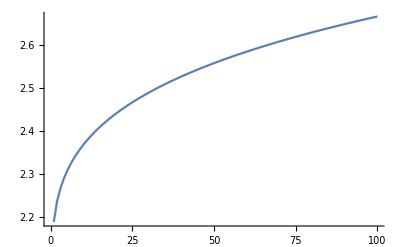

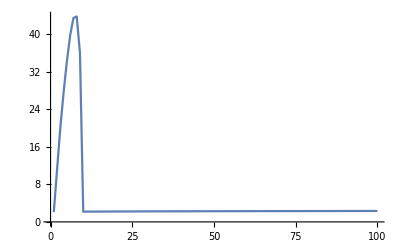

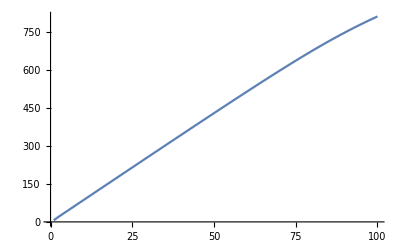

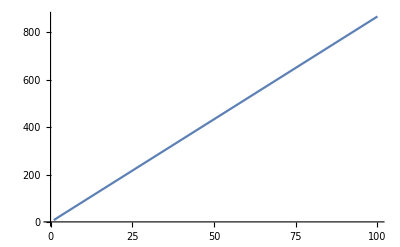

```mathematica
ListLinePlot[InvFitAcrossW270]
ListLinePlot[InvFitAcrossW280,PlotRange->All]
ListLinePlot[InvFitAcrossW290]
ListLinePlot[InvFitAcrossW300]
```

```mathematica
InvFitAcrossW275=Table[CalcInvFit[W,275,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW285=Table[CalcInvFit[W,285,0.9,0.9,1],{W,10,1000,10}];
```

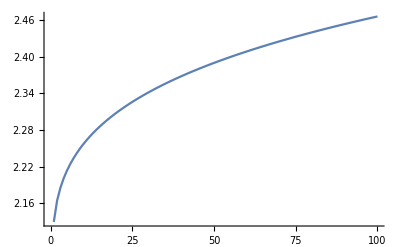

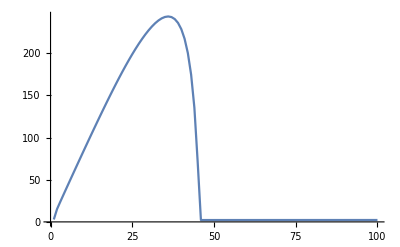

```mathematica
ListLinePlot[InvFitAcrossW275,PlotRange->All]
ListLinePlot[InvFitAcrossW285,PlotRange->All]
```

```mathematica
InvFitAcrossW285
```

{2.86521,15.2938,24.0143,32.5663,41.0645,49.5312,57.9716,66.3859,74.7721,83.1269,91.4458,99.7236,107.954,116.129,124.24,132.277,140.228,148.079,155.815,163.417,170.868,178.146,185.228,192.091,198.709,205.055,211.099,216.807,222.141,227.056,231.497,235.395,238.666,241.2,242.855,243.445,242.717,240.327,235.786,228.384,217.046,200.068,174.574,135.307,71.5263,2.19194,2.19301,2.19407,2.19512,2.19614,2.19715,2.19815,2.19913,2.2001,2.20106,2.202,2.20293,2.20384,2.20475,2.20564,2.20653,2.2074,2.20826,2.20911,2.20995,2.21079,2.21161,2.21242,2.21323,2.21402,2.21481,2.21559,2.21636,2.21713,2.21788,2.21863,2.21937,2.2201,2.22083,2.22155,2.22226,2.22297,2.22367,2.22436,2.22505,2.22573,2.22641,2.22708,2.22774,2.2284,2.22906,2.2297,2.23035,2.23098,2.23162,2.23224,2.23287,2.23349,2.2341,2.23471}

```mathematica
Equilibria=Function[{W,T,c,f,NTot},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};D1irValue=Re[D1irEq⟦4,1,2⟧/.allom/.pars];D1sValue=D1sEq⟦1,2⟧/.D1ir->D1irValue/.allom/.pars;NirValue=NirEq⟦1,2⟧/.{D1s->D1sValue,D1ir->D1irValue}/.allom/.pars;NsValue=NsEq⟦1,2⟧/.Nir->NirValue/.allom/.pars;PrValue=PrEq⟦1,2⟧/.{D1ir->D1irValue,D1s->D1sValue,Nir->NirValue}/.allom/.pars;{NsValue,NirValue,D1sValue,D1irValue,PrValue}];
```

```mathematica
Equilibria[400,285,0.9,0.9,1]
Equilibria[450,285,0.9,0.9,1]
Equilibria[500,285,0.9,0.9,1]
```

{0.183413,0.816587,0.00220181,0.000408801,0.026211}

{0.0223689,0.977631,0.00189653,0.000434161,0.232959}

{0.000509607,0.99949,0.0017321,0.000416207,9.64955}

The problem is that there are multiple equilibria, and I don’t know which one is the correct one to use. That may explain a lot of the goofiness in the response to temperature, if the stable equilibrium switches

```mathematica
D1irEquilibrium=Function[{W,T,c,f,NTot},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};D1irEq/.allom/.pars];
D1irEquilibrium[400,285,0.9,0.9,1]
```

{{D1ir→0},{D1ir→0.000469279+3.79471×10^-19 ⅈ},{D1ir→-0.0000540352+2.71051×10^-20 ⅈ},{D1ir→0.000408801-4.06576×10^-19 ⅈ}}

You can see from the numerical simulation that a different equilibrium is stable than what we were looking at in the analytical calculation.

```mathematica
W=400;T=285;f=0.9;NTot=1;
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};NumSol=NDSolve[({Ns'[t]==a1 (D1s[t]+D1ir[t])+a2 K2-β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t])Ns[t]-a2 K2 Ns[t],
Nir'[t]==β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t] NT,
D1ir'[t]==a1 D1s[t] Nir[t] NT-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β Ns[t] NT Pr[t]-γ Pr[t],
Ns[0]==0.1,
Nir[0]==0.9,
D1s[0]==0.1,
D1ir[0]==0,
Pr[0]==10}/.allom/.pars),
{Ns,Nir,D1s,D1ir,Pr},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
D1ir[1000]/.NumSol
```

{0.000469279}

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({Ns'[t]==a1 (D1s[t]+D1ir[t])+a2 K2-β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t])Ns[t]-a2 K2 Ns[t],
Nir'[t]==β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t] NT,
D1ir'[t]==a1 D1s[t] Nir[t] NT-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β Ns[t] NT Pr[t]-γ Pr[t],
Ns[0]==1,
Nir[0]==0,
D1s[0]==0.1,
D1ir[0]==0,
Pr[0]==1}/.allom/.pars),
{Ns,Nir,D1s,D1ir,Pr},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)/.{Ns->(Ns[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]]}/.D2s->K2/.allom/.pars
];
```

```mathematica
NumSolInvFit[400,285,0.9,0.9,1]
```

2.1852

```mathematica
CalcInvFit[400,270,0.9,0.9,1]
NumSolInvFit[400,270,0.9,0.9,1]
```

2.52744

2.52757

Here you can see the very large difference between the two calculations.

```mathematica
CalcInvFit[400,285,0.9,0.9,1]
NumSolInvFit[400,285,0.9,0.9,1]
```

228.384

2.1852

So, I need to recheck to see how the results change:

Now temperature only decreases the invasion fitness, just like with direct life cycle parasites.

```mathematica
Table[NumSolInvFit[400,T,0.9,0.9,1],{T,270,310,5}]
```

{2.52757,2.36788,2.2596,2.1852,2.13343,2.09694,2.07093,2.05218,2.03851}

```mathematica
InvFitAcrossW270=Table[NumSolInvFit[W,270,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW280=Table[NumSolInvFit[W,280,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW290=Table[NumSolInvFit[W,290,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW300=Table[NumSolInvFit[W,300,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW310=Table[NumSolInvFit[W,310,0.9,0.9,1],{W,10,1000,10}];
```

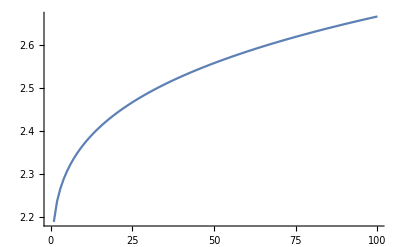

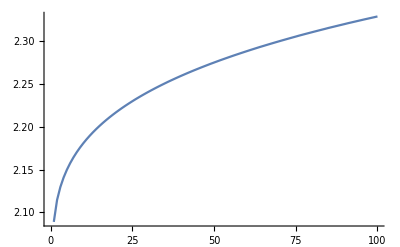

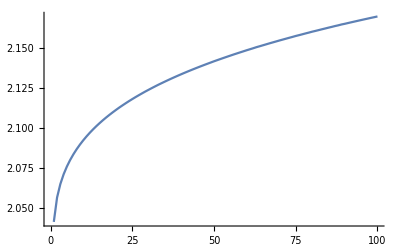

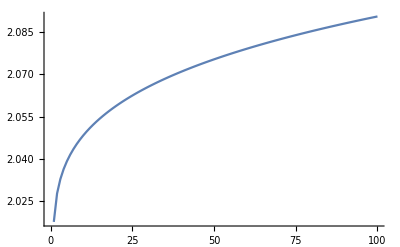

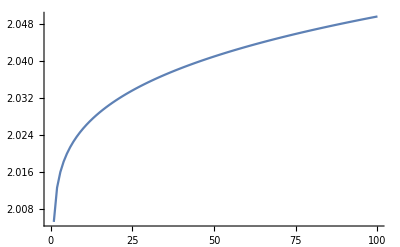

```mathematica
ListLinePlot[InvFitAcrossW270]
ListLinePlot[InvFitAcrossW280,PlotRange->All]
ListLinePlot[InvFitAcrossW290]
ListLinePlot[InvFitAcrossW300]
ListLinePlot[InvFitAcrossW310]
```

```mathematica
D1irEquilibrium=Function[{W,T,c,f,NTot},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};D1irEq/.allom/.pars];
```

```mathematica
CalcEquilibria=Function[{W,T,c,f,NTot,D1irValue},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars;
NirValue=NirEq[[1,2]]/.{D1s->D1sValue,D1ir->D1irValue}/.allom/.pars;
{NsEq[[1,2]]/.Nir->NirValue/.allom/.pars,
NirValue,
D1sValue,
PrEq[[1,2]]/.{D1ir->D1irValue,D1s->D1sValue,Nir->NirValue}/.allom/.pars}
];
```

```mathematica
CalcStability=Function[{W,T,c,f,NTot,i},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1irValue=D1irEq[[i,1,2]]/.allom/.pars;
Eqs=CalcEquilibria[W,T,c,f,NTot,D1irValue];
Eigenvalues[Jres/.{D1ir->D1irValue,D1s->Eqs[[3]],Nir->Eqs[[2]],Ns->Eqs[[1]],Pr->Eqs[[4]]}/.allom/.pars]
];
```

```mathematica
NumSolEquilibria=Function[{W,T,c,f,NTot},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({Ns'[t]==a1 (D1s[t]+D1ir[t])+a2 K2-β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t])Ns[t]-a2 K2 Ns[t],
Nir'[t]==β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t] NT,
D1ir'[t]==a1 D1s[t] Nir[t] NT-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β Ns[t] NT Pr[t]-γ Pr[t],
Ns[0]==1,
Nir[0]==0,
D1s[0]==0.1,
D1ir[0]==0,
Pr[0]==1}/.allom/.pars),
{Ns,Nir,D1s,D1ir,Pr},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
{Ns->(Ns[1000]/.Soln)[[1]],Nir->(Nir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],Pr->(Pr[1000]/.Soln)[[1]]}/.D2s->K2/.allom/.pars
];
```

Here we can confirm that everything agrees with everything else: for these parameters, you find that the second D_(1,I,r) equilibrium is stable and the fourth is unstable, and that the numerical solution goes to the second equilibrium.

```mathematica
(* Numerical calculation of equilibria *)
NumSolEquilibria[400,285,0.9,0.9,1]
(* Analytical calculation of D1ir equilibrium *)
D1irEquilibrium[400,285,0.9,0.9,1]
(* Analytical calculation of second equilibrium *)CalcEquilibria[400,285,0.9,0.9,1,D1irEquilibrium[400,285,0.9,0.9,1][[2,1,2]]]
(* Stability of the second equilibrium *)
CalcStability[400,285,0.9,0.9,1,2]
(* Analytical calculation of fourth equilibrium *)
CalcEquilibria[400,285,0.9,0.9,1,D1irEquilibrium[400,285,0.9,0.9,1][[4,1,2]]]
(* Stability of the fourth equilibrium *)
CalcStability[400,285,0.9,0.9,1,4]
```

{Ns→0.000631818,Nir→0.999368,D1s→0.00206527,D1ir→0.000469279,Pr→9.19172}

{{D1ir→0},{D1ir→0.000469279+3.79471×10^-19 ⅈ},{D1ir→-0.0000540352+2.71051×10^-20 ⅈ},{D1ir→0.000408801-4.06576×10^-19 ⅈ}}

{0.000631785-1.23129×10^-15 ⅈ,0.999368+1.23129×10^-15 ⅈ,0.00206527-8.74519×10^-19 ⅈ,9.19219+1.79252×10^-11 ⅈ}

{-0.919824-1.79268×10^-12 ⅈ,-0.438465+0.183501 ⅈ,-0.438465-0.183501 ⅈ,-0.00999509-1.926×10^-17 ⅈ,-0.000581116+4.95048×10^-20 ⅈ}

{0.183413+1.146×10^-15 ⅈ,0.816587-1.146×10^-15 ⅈ,0.00220181+9.002×10^-19 ⅈ,0.026211-1.98358×10^-16 ⅈ}

{-0.441139-0.17397 ⅈ,-0.441139+0.17397 ⅈ,-0.0553977-1.96213×10^-16 ⅈ,0.0223926+8.84837×10^-17 ⅈ,-0.000588722-4.93624×10^-20 ⅈ}

Whereas for these parameters, you find that the fourth D_(1,I,r) equilibrium is stable and the second is unstable, and that the numerical solution goes to the fourth equilibrium.

```mathematica
(* Numerical calculation of equilibria *)
NumSolEquilibria[400,270,0.9,0.9,1]
(* Analytical calculation of D1ir equilibrium *)
D1irEquilibrium[400,270,0.9,0.9,1]
(* Analytical calculation of second equilibrium *)CalcEquilibria[400,270,0.9,0.9,1,D1irEquilibrium[400,270,0.9,0.9,1][[2,1,2]]]
(* Stability of the second equilibrium *)
CalcStability[400,270,0.9,0.9,1,2]
(* Analytical calculation of fourth equilibrium *)
CalcEquilibria[400,270,0.9,0.9,1,D1irEquilibrium[400,270,0.9,0.9,1][[4,1,2]]]
(* Stability of the fourth equilibrium *)
CalcStability[400,270,0.9,0.9,1,4]
```

{Ns→0.0008184,Nir→0.999182,D1s→0.00451343,D1ir→0.00283781,Pr→20.0466}

{{D1ir→0},{D1ir→0.00569843+3.03577×10^-18 ⅈ},{D1ir→-0.000030503+2.81893×10^-18 ⅈ},{D1ir→0.00283781-5.85469×10^-18 ⅈ}}

{-273.334-4.71654×10^-11 ⅈ,274.334+4.71654×10^-11 ⅈ,0.0000330099-5.65771×10^-18 ⅈ,-0.0148539+1.19746×10^-17 ⅈ}

{-27.4323-4.71672×10^-12 ⅈ,27.3249+4.71654×10^-12 ⅈ,-0.343991+5.01589×10^-16 ⅈ,-0.00147998+2.62194×10^-19 ⅈ,-0.00147434-1.48769×10^-18 ⅈ}

{0.000818357+3.90343×10^-15 ⅈ,0.999182-3.90343×10^-15 ⅈ,0.00451343+8.3206×10^-18 ⅈ,20.0476-9.56992×10^-11 ⅈ}

{-2.00648+9.56962×10^-12 ⅈ,-0.318074-0.111201 ⅈ,-0.318074+0.111201 ⅈ,-0.00999514+4.64646×10^-17 ⅈ,-0.00164196-2.46591×10^-19 ⅈ}

#### True predator-prey model

```mathematica
dNsdt=rN (Ns+Nir) (1-(Ns+Nir)/KN)-β Ns Pr-a1 (D1s+D1ir) Ns;
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir ;
dD1sdt=b a1 (D1s+D1ir) (Ns+Nir)-a1 D1s Nir-μ1 D1s;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

Before going any further, notice that the dynamics of the total predator population depend only on the total predator population and the total prey population. Thus we can solve directly for the total prey population at equilibrium.

```mathematica
Simplify[dD1sdt+dD1irdt]
Solve[((dD1sdt+dD1irdt)/.Ns->Ntot-Nir)==0,Ntot]
```

(D1ir+D1s) (a1 b (Nir+Ns)-μ1)

{{Ntot→μ1/(a1 b)}}

From this, you can see that the equilibrium total prey population will be N_S+N_(I,r)=μ_1/(b a_1). At the same time, the dynamics of the total prey population depend only on the total predator and prey populations, so we can also find for the total predator population at equililbrium.

```mathematica
Simplify[dNsdt+dNirdt]
Solve[(dNsdt+dNirdt/.D1s->Dtot-D1ir/.Ns->μ1/(b a1)-Nir)==0,Dtot]
```

-((Nir+Ns) (a1 (D1ir+D1s) KN+(-KN+Nir+Ns) rN))/KN

{{Dtot→(rN (a1 b KN-μ1))/(a1^2 b KN)}}

This greatly simplifies the dynamics, as we can drop two equations from the systemN_S completely (it is determined entirely by the equilibrium for N_(I,r)) and we can replace N_S+N_(I,r) with μ_1/(b a_1) everywhere else.

Notice that this really simplifies the dynamics of D_(1,S) in particular, from (dD_(1,S))/dt=b a_1(D_(1,S)+D_(1I,r))(N_S+N_(I,r))-a_1 D_(1,S)N_(I,r)-μ_1 D_(1,S)=μ_1(D_(1,S)+D_(1I,r))-a_1 D_(1,S)N_(I,r)-μ_1 D_(1,S)=μ_1 D_(1I,r)-a_1 D_(1,S)N_(I,r)

```mathematica
dNirdt=dNirdt/.{Ns->μ1/(a1 b)-Nir}/.{D1s->(rN (a1 b KN-μ1))/(a1^2 b KN)-D1ir}
dD1irdt=dD1irdt/.{D1s->(rN (a1 b KN-μ1))/(a1^2 b KN)-D1ir}
dPrdt=λ1 D1ir-β Ns Pr-γ Pr/.{Ns->μ1/(a1 b)-Nir}
```

-(Nir rN (a1 b KN-μ1))/(a1 b KN)+Pr β (-Nir+μ1/(a1 b))

a1 Nir (-D1ir+(rN (a1 b KN-μ1))/(a1^2 b KN))-D1ir μ1

-Pr γ+D1ir λ1-Pr β (-Nir+μ1/(a1 b))

```mathematica
Simplify[Solve[{dNirdt==0,dD1irdt==0,dPrdt==0},{Nir,D1ir,Pr}]]
```

{{Nir→0,D1ir→0,Pr→0},{Nir→(a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))/(2 a1^2 b β),D1ir→1/(4 a1^4 b^2 (1+b) KN β^2 λ1 μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1+a1 β μ1+a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))),Pr→1/(4 a1^4 b^2 (1+b) KN β^2 γ μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1-a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))},{Nir→(a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))/(2 a1^2 b β),D1ir→1/(4 a1^4 b^2 (1+b) KN β^2 λ1 μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1+a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))),Pr→-1/(4 a1^4 b^2 (1+b) KN β^2 γ μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (-a1^2 b γ-a1 b β λ1+a1 β μ1+a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))}}

```mathematica
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir ;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

-((Nir+Ns) (a1 (D1ir+D1s) KN+(-KN+Nir+Ns) rN))/KN

{{Dtot→(rN (a1 b KN-μ1))/(a1^2 b KN)}}

```mathematica
dNirdt=β (μ1/(b a1)-Nir) Pr-a1 (D1s+D1ir) Nir ;
dD1sdt=μ1 D1ir-a1 D1s Nir;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

```mathematica
D1sEq=Simplify[Solve[dNirdt==0,D1s]]
```

{{D1s→-D1ir+(Pr β (-a1 b Nir+μ1))/(a1^2 b Nir)}}

```mathematica
D1irEq=Solve[dPrdt==0,D1ir][[1]]
```

{D1ir→(Ns Pr β+Pr γ)/λ1}

```mathematica
NirEq=Solve[(dD1irdt/.D1irEq)==0,Nir][[1]]
```

{Nir→((Ns Pr β+Pr γ) μ1)/(a1 D1s λ1)}

```mathematica
D1sEq=Solve[(dD1sdt/.NirEq/.D1irEq)==0,D1s][[2]]
```

{D1s→-(-b Ns Pr β μ1-b Pr γ μ1)/(λ1 (-a1 b Ns+μ1))}

```mathematica
NsEq=Solve[Simplify[dNirdt/.D1irEq/.NirEq/.D1sEq]==0,Ns][[2]]
```

{Ns→(-a1 b γ-b β λ1+β μ1+b β μ1+√((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))/(2 a1 b β)}

```mathematica
Solve[Numerator[Together[dNsdt/.D1irEq/.NirEq/.D1sEq/.NsEq]]==0,Pr][[1]]
```

{Pr→(-a1^2 b^2 KN rN γ μ1-a1 b^2 KN rN β λ1 μ1-a1 b KN rN β μ1^2+a1 b^2 KN rN β μ1^2+a1 b rN γ μ1^2+b rN β λ1 μ1^2+rN β μ1^3-b rN β μ1^3+a1 b KN rN μ1 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1))-rN μ1^2 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))/(a1^2 b^2 KN β γ μ1+a1 b^2 KN β^2 λ1 μ1-a1 b KN β^2 μ1^2-a1 b^2 KN β^2 μ1^2-a1 b KN β μ1 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))}

```mathematica
K
```

K

```mathematica
dX=r X (1-X/K)-a X Y;
dY=b X Y-m Y;
```

```mathematica
Solve[dY==0,X]
Solve[dX==0,Y]/.{X->m/b}//Simplify
```

{{X→m/b}}

{{Y→((K-m/b) r)/(a K)}}